## VQE analysis and plots for the chemistry-stuff paper

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Set the chemical accuracy!

```mathematica
chemacc=1.59*10^-3
```

0.00159

## Modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit (Daniel's format). Returns {hamiltonian, nterms, nqubits}.";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits,a},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}->Subscript[Id, 0] a};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]

SetAttributes[PrintTables,HoldRest]
PrintTables[molecule_,data_]:=With[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
trial=1;
disp=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
res⟦3⟧,
ϵgs<=chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦4⟧⟦"ansatz"⟧],
ToString[res⟦4⟧⟦"E"⟧],
ToString[res⟦-2⟧]
}
,{res,results}];
PrependTo[disp,{"trial","runtime(min)","chemacc?","ϵgs","ngates", "elims","fevs","ngates/cycle","<E>/cycle","aborted cycle"}];
DestroyAllQuregs[];
Print@TextGrid[disp,Frame->All]
]

GetSuccData[molecule_]:=Module[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule],
filtered={}
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
If[ϵgs<=chemacc,
 AppendTo[filtered,res]
]
,{res,results}];
DestroyAllQuregs[];
filtered
]

CountGates::usage="CountGates[circuit], return the count for {doubles, singles}";
CountGates[circuit_]:=Module[{doubles},
doubles=Count[circuit/.{Subscript[C, _][_]->2,Subscript[_, _]-> 1,Subscript[_, _][_]->1},2];
{doubles,Length@circuit-doubles}
]
```

## Load results, hamiltonians, labels, groundstate,occupations

```mathematica
SetDirectory["~/chemistry-code/vqe/hamiltonians"];
hamiltonians=<|"BeH2"->FormatHamiltonian["hamiltonian-beh2.txt"],"LiH"->FormatHamiltonian["hamiltonian-lih.txt"],"H2O"->FormatHamiltonian["hamiltonian-h2o.txt"],"H2"->FormatHamiltonian["hamiltonian-h2.txt"],"H3"->FormatHamiltonian["hamiltonian-h3.txt"],
"H4"->FormatHamiltonian["hamiltonian-h4.txt"],"He2H"->FormatHamiltonian["hamiltonian-he2h.txt"],"He3H"->FormatHamiltonian["hamiltonian-he3h.txt"]|>;
labels=<|"BeH2"->"BeH_2","LiH"->"LiH","H2O"->"H_2O","H2"->"H_2","H4"->"H_4","H3"->"H_3","He2H"->TraditionalForm["He_2H^+"],"He3H"->TraditionalForm@"He_3H^+"|>;
groundstates=<|"H2O"->-75.01402200471308,"LiH"->-7.882059857867098,"H2"->-1.1372838344885023,"H4"->-1.9961503255188098,"He2H"->-5.769926974270885,"He3H"->-8.575314719616504,"BeH2"->-15.5951755114264,"H3"->-1.4198925029235445|>;
occupations=<|"BeH2"->6,"LiH"->4,"H2O"->10,"H2"->2,"H3"->3,"H4"->4,"He2H"->5,"He3H"->7|>;
nqubits=<|"BeH2"->14,"LiH"->12,"H2O"->14,"H2"->4,"H3"->6,"H4"->8,"He2H"->6,"He3H"->8|>;
```

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}

```mathematica
SetDirectory["~/chemistry-code/vqe/results"];
resBeH2<<resBeH2.mx;
resLiH<<resLiH.mx;
resH2O<<resH2O.mx;
resH2<<resH2.mx;
resH4<<resH4.mx;
resH3<<resH3.mx;
resHe3H<<resHe3H.mx;
resHe2H<<resHe2H.mx;
data=<||>;
data["BeH2"]=resBeH2;
data["LiH"]=resLiH;
data["H2O"]=resH2O;
data["H2"]=resH2;
data["H4"]=resH4;
data["H3"]=resH3;
data["He2H"]=resHe2H;
data["He3H"]=resHe3H;
```

```mathematica
molecules={"H2","He2H","He3H","H3","LiH","H4","H2O","BeH2"}
```

{H2,He2H,He3H,H3,LiH,H4,H2O,BeH2}

## Tables

### Full results

Table[Print[labels[mol]]; PrintTables[mol, data], {mol, Keys@hamiltonians}];

BeH_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 446.065 | True | 0.000786197 | 89 | {3, 1, 240, 1150} | 72384 | {0, 5, 10, 15, 22, 28, 30, 23, 33, 37, 27, 40, 49, 46, 65, 74, 89, 89} | {-15.5603, -15.5633, -15.5693, -15.5695, -15.5735, -15.5753, -15.5755, -15.5801, -15.5803, -15.5804, -15.5828, -15.5831, -15.5833, -15.5934, -15.5941, -15.5942, -15.5944, -15.5944} | {}
2 | 228.247 | True | 0.00109689 | 62 | {0, 0, 66, 724} | 35429 | {0, 18, 12, 17, 30, 35, 48, 51, 62, 62} | {-15.5603, -15.5626, -15.5656, -15.5684, -15.5768, -15.5805, -15.5894, -15.5936, -15.5941, -15.5941} | {}
3 | 471.871 | True | 0.000669187 | 104 | {5, 2, 126, 963} | 74426 | {0, 16, 15, 18, 26, 32, 38, 50, 69, 74, 82, 94, 104, 104} | {-15.5603, -15.5663, -15.5688, -15.5734, -15.5761, -15.5789, -15.5816, -15.582, -15.5849, -15.5931, -15.594, -15.5943, -15.5945, -15.5945} | {}
4 | 35.3696 | True | 0.000891144 | 77 | {1, 0, 170, 772} | 46754 | {0, 8, 14, 16, 25, 31, 47, 47, 49, 59, 77, 77} | {-15.5603, -15.5664, -15.5689, -15.5722, -15.5762, -15.579, -15.5815, -15.5819, -15.5893, -15.5938, -15.5943, -15.5943} | {}
5 | 743.145 | True | 0.000997642 | 75 | {4, 0, 165, 1004} | 56681 | {0, 11, 15, 21, 22, 25, 27, 35, 38, 43, 57, 69, 75, 75} | {-15.5603, -15.5663, -15.5702, -15.5736, -15.5751, -15.5775, -15.5783, -15.5785, -15.5833, -15.5886, -15.5934, -15.594, -15.5942, -15.5942} | {}
6 | 415.241 | False | 0.00310257 | 74 | {4, 1, 255, 764} | 55246 | {0, 21, 22, 27, 44, 42, 43, 47, 35, 48, 55, 74, 74} | {-15.5603, -15.5669, -15.5756, -15.5764, -15.5766, -15.5789, -15.581, -15.5813, -15.5905, -15.5911, -15.5919, -15.5921, -15.5921} | {}
7 | 269.037 | True | 0.00107556 | 71 | {2, 1, 206, 822} | 48528 | {0, 8, 14, 21, 33, 43, 44, 43, 51, 53, 71, 71} | {-15.5603, -15.5636, -15.5733, -15.5738, -15.5769, -15.5824, -15.586, -15.5898, -15.5917, -15.5939, -15.5941, -15.5941} | {2}
8 | 297.075 | True | 0.00107872 | 58 | {0, 0, 288, 770} | 55130 | {0, 14, 19, 19, 26, 35, 42, 37, 38, 44, 51, 49, 58, 58} | {-15.5603, -15.5683, -15.5714, -15.5758, -15.5839, -15.584, -15.5865, -15.5892, -15.5894, -15.5917, -15.5919, -15.5939, -15.5941, -15.5941} | {}
9 | 486.603 | True | 0.000668278 | 114 | {1, 0, 207, 919} | 69542 | {0, 13, 19, 18, 21, 33, 44, 40, 46, 54, 55, 90, 114, 114} | {-15.5603, -15.5669, -15.5706, -15.5725, -15.5764, -15.5787, -15.579, -15.5812, -15.5895, -15.5924, -15.5939, -15.5943, -15.5945, -15.5945} | {}
10 | 55.8 | False | 0.017846 | 18 | {0, 0, 66, 172} | 6159 | {0, 7, 13, 18, 18} | {-15.5603, -15.5664, -15.5706, -15.5773, -15.5773} | {}

LiH

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 59.2913 | True | 0.00132602 | 23 | {0, 102, 56, 69} | 7112 | {0, 8, 7, 16, 23, 23} | {-7.86136, -7.8761, -7.87804, -7.88043, -7.88073, -7.88073} | {}
2 | 23.8022 | False | 0.0040206 | 12 | {0, 28, 29, 81} | 2938 | {0, 10, 12, 12} | {-7.86136, -7.87612, -7.87804, -7.87804} | {4}
3 | 82.2815 | True | 0.00143326 | 24 | {1, 195, 42, 118} | 9580 | {0, 6, 9, 8, 12, 15, 24, 24} | {-7.86136, -7.86218, -7.86384, -7.87801, -7.87979, -7.88044, -7.88063, -7.88063} | {9}
4 | 6.86707 | False | 0.0207014 | 0 | {0, 0, 0, 0} | 785 | {0, 0} | {-7.86136, -7.86136} | {1, 2}
5 | 13.9845 | False | 0.00402039 | 8 | {1, 25, 0, 66} | 1801 | {0, 8, 8} | {-7.86136, -7.87804, -7.87804} | {2}
6 | 64.0422 | True | 0.00144262 | 20 | {1, 92, 92, 75} | 8606 | {0, 10, 12, 15, 20, 20} | {-7.86136, -7.87807, -7.87841, -7.88039, -7.88062, -7.88062} | {}
7 | 53.7304 | False | 0.00160868 | 17 | {1, 98, 100, 64} | 6754 | {0, 8, 10, 15, 17, 17} | {-7.86136, -7.8761, -7.87804, -7.8791, -7.88045, -7.88045} | {}
8 | 25.1661 | False | 0.00401906 | 9 | {0, 43, 53, 45} | 3172 | {0, 7, 9, 9} | {-7.86136, -7.8761, -7.87804, -7.87804} | {}
9 | 277.232 | True | 0.000503547 | 35 | {1, 229, 18, 313} | 25909 | {0, 10, 13, 18, 21, 26, 36, 35, 35} | {-7.86136, -7.8761, -7.8767, -7.87859, -7.88025, -7.88104, -7.88124, -7.88156, -7.88156} | {}
10 | 94.1075 | True | 0.000995581 | 23 | {2, 156, 43, 117} | 11145 | {0, 17, 11, 15, 20, 23, 23} | {-7.86136, -7.8762, -7.87804, -7.87863, -7.88088, -7.88106, -7.88106} | {}

H_2O

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 60 x | True | 0.0015335 | 86 | {0, 0, 167, 905} | 97633 | {0, 20, 24, 36, 39, 44, 49, 59, 68, 73, 76, 75, 79, 89, 86, 86} | {-74.9638, -74.9824, -74.9868, -74.9938, -74.9963, -75.0014, -75.004, -75.0061, -75.0084, -75.0095, -75.0112, -75.0115, -75.0119, -75.0123, -75.0125, -75.0125} | {}
2 | 1506.21 | False | 0.00171029 | 96 | {1, 1, 237, 1038} | 92652 | {0, 7, 11, 13, 15, 27, 35, 39, 48, 47, 51, 52, 57, 65, 73, 79, 85, 96, 96} | {-74.9638, -74.9766, -74.9783, -74.98, -74.9844, -74.9889, -74.9934, -74.9975, -75.0036, -75.0053, -75.0067, -75.009, -75.0093, -75.01, -75.011, -75.0118, -75.0121, -75.0123, -75.0123} | {}
3 | 2418.44 | True | 0.0014174 | 103 | {2, 0, 198, 1255} | 129132 | {0, 24, 34, 32, 35, 42, 42, 52, 58, 58, 65, 78, 90, 83, 90, 97, 103, 103} | {-74.9638, -74.9773, -74.9855, -74.9901, -74.9931, -74.9947, -75.0002, -75.0009, -75.0049, -75.0083, -75.0098, -75.0105, -75.0107, -75.0117, -75.0122, -75.0124, -75.0126, -75.0126} | {}
4 | 1981.21 | False | 0.00175573 | 119 | {1, 1, 88, 1209} | 104850 | {0, 14, 26, 29, 33, 32, 41, 45, 53, 56, 67, 68, 87, 98, 109, 119, 119} | {-74.9638, -74.9778, -74.9804, -74.9838, -74.986, -74.9862, -74.9874, -74.9909, -74.9923, -74.9933, -74.9935, -75.0059, -75.0089, -75.0108, -75.0113, -75.0123, -75.0123} | {}
5 | 1360.8 | False | 0.0026217 | 85 | {0, 0, 93, 971} | 79204 | {0, 7, 22, 28, 39, 41, 48, 54, 65, 77, 70, 75, 85, 85} | {-74.9638, -74.9681, -74.9742, -74.9922, -74.9944, -74.9983, -75.0016, -75.0044, -75.0062, -75.0071, -75.0103, -75.0112, -75.0114, -75.0114} | {}
6 | 1235.63 | False | 0.00159058 | 88 | {1, 0, 182, 860} | 76320 | {0, 6, 11, 17, 26, 29, 40, 45, 57, 69, 62, 65, 68, 80, 88, 88} | {-74.9638, -74.9766, -74.9794, -74.9835, -74.9872, -74.9913, -74.9982, -75.0033, -75.0063, -75.0073, -75.0096, -75.0098, -75.012, -75.0122, -75.0124, -75.0124} | {}
7 | 218.536 | False | 0.0208635 | 34 | {0, 0, 35, 267} | 16349 | {0, 21, 25, 27, 34, 34} | {-74.9638, -74.9828, -74.9855, -74.9928, -74.9932, -74.9932} | {}
8 | 750.734 | False | 0.012768 | 59 | {0, 0, 148, 682} | 50403 | {0, 6, 13, 19, 25, 30, 35, 39, 44, 53, 57, 59, 59} | {-74.9638, -74.9681, -74.9714, -74.9743, -74.9762, -74.9799, -74.9924, -74.9951, -74.9987, -75.0005, -75.0011, -75.0013, -75.0013} | {}
9 | 1780.96 | True | 0.000575987 | 98 | {1, 0, 186, 1159} | 106765 | {0, 7, 17, 20, 25, 35, 32, 37, 40, 43, 58, 63, 72, 79, 82, 88, 79, 91, 98, 98} | {-74.9638, -74.9766, -74.9808, -74.9831, -74.9833, -74.9849, -74.9921, -74.9963, -74.9981, -74.9991, -75.0071, -75.0099, -75.0106, -75.0119, -75.0121, -75.0123, -75.0127, -75.0132, -75.0134, -75.0134} | {}
10 | 1598.03 | False | 0.0113934 | 84 | {1, 1, 0, 1163} | 90004 | {0, 40, 22, 27, 38, 43, 44, 54, 58, 71, 75, 82, 80, 84, 84} | {-74.9638, -74.9806, -74.983, -74.9851, -74.9897, -74.9911, -74.9939, -74.9942, -74.9971, -75.0009, -75.0017, -75.002, -75.0024, -75.0026, -75.0026} | {16, 17}
11 | 94.1075 | False | 0.0128035 | 54 | {2, 1, 190, 664} | 45249 | {0, 32, 16, 19, 22, 34, 32, 36, 47, 37, 54, 54} | {-74.9638, -74.9766, -74.9823, -74.9863, -74.9878, -74.994, -74.9986, -74.9992, -74.9997, -75.001, -75.0012, -75.0012} | {}

H_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 2.64941 | True | 8.19798×10^-11 | 7 | {0, 6, 3, 23} | 1802 | {0, 7, 7} | {-1.11676, -1.13728, -1.13728} | {2, 3}
2 | 2.97535 | True | 1.92396×10^-9 | 6 | {0, 10, 7, 17} | 1543 | {0, 6, 6} | {-1.11676, -1.13728, -1.13728} | {}
3 | 3.46747 | True | 2.12245×10^-8 | 5 | {0, 9, 4, 22} | 1718 | {0, 5, 5} | {-1.11676, -1.13728, -1.13728} | {}
4 | 1.55093 | True | 1.3614×10^-11 | 4 | {0, 10, 14, 10} | 1106 | {0, 4, 4} | {-1.11676, -1.13728, -1.13728} | {2}
5 | 3.16627 | True | 2.99177×10^-9 | 4 | {0, 4, 3, 29} | 1493 | {0, 4, 4} | {-1.11676, -1.13728, -1.13728} | {}
6 | 2.38002 | True | 4.53914×10^-10 | 5 | {0, 12, 8, 15} | 1234 | {0, 5, 5} | {-1.11676, -1.13728, -1.13728} | {}
7 | 2.24351 | True | 3.24378×10^-10 | 7 | {0, 6, 10, 16} | 1177 | {0, 7, 7} | {-1.11676, -1.13728, -1.13728} | {}
8 | 2.42319 | True | 1.34938×10^-8 | 8 | {0, 3, 1, 26} | 1490 | {0, 8, 8} | {-1.11676, -1.13728, -1.13728} | {}
9 | 3.3637 | True | 3.44705×10^-9 | 6 | {0, 3, 6, 25} | 1800 | {0, 6, 6} | {-1.11676, -1.13728, -1.13728} | {}
10 | 3.12226 | True | 2.45106×10^-9 | 8 | {0, 2, 5, 25} | 1709 | {0, 10, 8} | {-1.11676, -1.13728, -1.13728} | {}

H_3

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 560.877 | True | 1.32508×10^-7 | 16 | {2, 40, 6, 31} | 5069 | {0, 12, 17, 16, 16} | {-1.33201, -1.41786, -1.41965, -1.41989, -1.41989} | {4, 5}
2 | 546.428 | True | 5.04679×10^-7 | 16 | {0, 41, 25, 44} | 5891 | {0, 9, 12, 15, 16, 16} | {-1.33201, -1.40089, -1.40117, -1.41877, -1.41989, -1.41989} | {}
3 | 511.77 | True | 2.21889×10^-6 | 15 | {0, 32, 18, 47} | 4809 | {0, 14, 12, 15, 15} | {-1.33201, -1.39239, -1.41786, -1.41989, -1.41989} | {}
4 | 300.3 | True | 1.50065×10^-6 | 13 | {0, 43, 14, 28} | 3281 | {0, 8, 11, 13, 13} | {-1.33201, -1.41786, -1.41971, -1.41989, -1.41989} | {}
5 | 263.215 | True | 6.60757×10^-7 | 11 | {0, 25, 19, 15} | 2789 | {0, 11, 11, 11} | {-1.33201, -1.41786, -1.41989, -1.41989} | {}
6 | 335.753 | True | 2.27095×10^-7 | 17 | {0, 35, 18, 26} | 3380 | {0, 6, 10, 17, 17} | {-1.33201, -1.39135, -1.41786, -1.41989, -1.41989} | {}
7 | 264.104 | True | 4.02632×10^-7 | 20 | {0, 16, 1, 3} | 2426 | {0, 20, 20} | {-1.33201, -1.41989, -1.41989} | {}
8 | 320.173 | True | 2.02853×10^-7 | 19 | {0, 13, 2, 6} | 2951 | {0, 19, 19} | {-1.33201, -1.41989, -1.41989} | {2, 3}
9 | 307.642 | True | 3.64713×10^-7 | 15 | {0, 13, 0, 12} | 2927 | {0, 15, 15} | {-1.33201, -1.41989, -1.41989} | {}
10 | 330.431 | True | 4.93773×10^-6 | 12 | {0, 36, 8, 15} | 3034 | {0, 8, 12, 12} | {-1.33201, -1.41786, -1.41989, -1.41989} | {}

H_4

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 10961.9 | True | 0.000107323 | 46 | {0, 186, 55, 105} | 37928 | {0, 10, 14, 18, 22, 24, 28, 34, 39, 37, 39, 45, 46, 46} | {-1.82914, -1.89384, -1.89742, -1.92212, -1.95402, -1.95761, -1.96358, -1.98302, -1.98433, -1.99443, -1.99496, -1.99516, -1.99604, -1.99604} | {}
2 | 13532.2 | False | 0.00609807 | 58 | {0, 180, 34, 94} | 45613 | {0, 14, 19, 18, 26, 26, 34, 37, 43, 49, 53, 54, 58, 58} | {-1.82914, -1.87811, -1.90868, -1.91201, -1.93155, -1.95967, -1.96064, -1.98148, -1.98487, -1.98725, -1.98749, -1.98966, -1.99005, -1.99005} | {}
3 | 15817.7 | True | 0.000321675 | 67 | {0, 144, 43, 113} | 48857 | {0, 10, 9, 17, 24, 25, 33, 37, 47, 54, 58, 65, 67, 67} | {-1.82914, -1.87511, -1.90691, -1.93744, -1.95853, -1.97557, -1.97641, -1.98878, -1.9942, -1.99508, -1.99543, -1.99562, -1.99583, -1.99583} | {}
4 | 2932.47 | False | 0.0381272 | 33 | {0, 94, 54, 37} | 12832 | {0, 7, 10, 12, 13, 17, 26, 33, 33} | {-1.82914, -1.87511, -1.88898, -1.89771, -1.91289, -1.95238, -1.9575, -1.95802, -1.95802} | {}
5 | 3244.49 | False | 0.017934 | 29 | {0, 91, 55, 42} | 14741 | {0, 10, 10, 14, 18, 19, 26, 29, 29} | {-1.82914, -1.87486, -1.90692, -1.93439, -1.97358, -1.97643, -1.97785, -1.97822, -1.97822} | {}
6 | 11628.3 | True | 0.00013928 | 63 | {2, 147, 31, 85} | 37004 | {0, 14, 19, 20, 23, 25, 30, 36, 43, 54, 63, 63} | {-1.82914, -1.89408, -1.9758, -1.97633, -1.97708, -1.97756, -1.97817, -1.98827, -1.99486, -1.99568, -1.99601, -1.99601} | {}
7 | 15083.1 | True | 0.0000980405 | 62 | {0, 165, 55, 136} | 48623 | {0, 10, 11, 21, 24, 25, 22, 26, 33, 39, 44, 54, 56, 62, 62} | {-1.82914, -1.87582, -1.90692, -1.91733, -1.92443, -1.9471, -1.97106, -1.97729, -1.98359, -1.99444, -1.99497, -1.99541, -1.99579, -1.99604, -1.99605} | {}
8 | 16807.2 | True | 0.0000906318 | 56 | {0, 221, 79, 172} | 54202 | {0, 11, 12, 14, 23, 26, 19, 20, 23, 25, 29, 34, 31, 41, 39, 49, 56, 56} | {-1.82914, -1.87639, -1.89251, -1.93026, -1.93696, -1.96314, -1.97602, -1.97673, -1.97764, -1.97811, -1.97829, -1.97852, -1.98631, -1.98725, -1.9949, -1.99568, -1.99606, -1.99606} | {}
9 | 3331.62 | False | 0.101728 | 34 | {0, 92, 27, 36} | 13678 | {0, 7, 10, 14, 19, 28, 34, 34} | {-1.82914, -1.84788, -1.86618, -1.86717, -1.89331, -1.89417, -1.89442, -1.89442} | {}
10 | 8833.18 | True | 0.0000900342 | 46 | {1, 143, 78, 71} | 31488 | {0, 4, 11, 14, 22, 30, 32, 37, 31, 34, 43, 46, 46} | {-1.82914, -1.84817, -1.85163, -1.90057, -1.9099, -1.92892, -1.93092, -1.93109, -1.96421, -1.9921, -1.99553, -1.99606, -1.99606} | {}

He_2H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 137.704 | True | 3.89252×10^-8 | 15 | {0, 9, 0, 6} | 1352 | {0, 15, 15} | {-5.76412, -5.76993, -5.76993} | {2, 3}
2 | 74.8069 | True | 1.14984×10^-9 | 4 | {0, 5, 7, 14} | 795 | {0, 4, 4} | {-5.76412, -5.76993, -5.76993} | {2, 3}
3 | 68.191 | True | 2.28789×10^-8 | 6 | {1, 11, 0, 12} | 762 | {0, 6, 6} | {-5.76412, -5.76993, -5.76993} | {2, 3}
4 | 91.9499 | True | 9.05341×10^-8 | 5 | {0, 8, 7, 10} | 1071 | {0, 5, 5} | {-5.76412, -5.76993, -5.76993} | {}
5 | 79.869 | True | 3.33728×10^-8 | 5 | {0, 12, 9, 4} | 915 | {0, 5, 5} | {-5.76412, -5.76993, -5.76993} | {2, 3}
6 | 159.302 | True | 1.5852×10^-8 | 13 | {0, 6, 0, 11} | 1966 | {0, 13, 13} | {-5.76412, -5.76993, -5.76993} | {2, 3}
7 | 103.037 | True | 4.29978×10^-8 | 6 | {0, 6, 0, 16} | 1120 | {0, 6, 6} | {-5.76412, -5.76993, -5.76993} | {2, 3}
8 | 77.0516 | True | 4.35207×10^-14 | 2 | {0, 9, 6, 13} | 1188 | {0, 2, 2} | {-5.76412, -5.76993, -5.76993} | {2, 3}
9 | 91.7435 | True | 3.84809×10^-7 | 4 | {0, 9, 7, 9} | 966 | {0, 4, 4} | {-5.76412, -5.76993, -5.76993} | {}
10 | 77.0602 | True | 8.22264×10^-9 | 4 | {0, 9, 15, 0} | 818 | {0, 4, 4} | {-5.76412, -5.76993, -5.76993} | {2, 3}

He_3H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 271.455 | True | 1.08709×10^-6 | 8 | {0, 11, 0, 21} | 1520 | {0, 8, 8} | {-8.56935, -8.57531, -8.57531} | {}
2 | 196.977 | True | 1.83132×10^-6 | 5 | {0, 9, 10, 16} | 1081 | {0, 5, 5} | {-8.56935, -8.57531, -8.57531} | {}
3 | 166.376 | True | 0.000041779 | 3 | {0, 11, 0, 25} | 897 | {0, 3, 3} | {-8.56935, -8.57527, -8.57527} | {}
4 | 296.873 | True | 7.26018×10^-6 | 6 | {2, 6, 5, 20} | 1657 | {0, 6, 6} | {-8.56935, -8.57531, -8.57531} | {}
5 | 260.813 | True | 2.43238×10^-6 | 10 | {0, 10, 9, 11} | 1460 | {0, 10, 10} | {-8.56935, -8.57531, -8.57531} | {}
6 | 262.57 | True | 0.0000111235 | 5 | {0, 15, 0, 20} | 1555 | {0, 5, 5} | {-8.56935, -8.5753, -8.5753} | {}
7 | 324.083 | True | 4.05198×10^-7 | 10 | {0, 8, 0, 22} | 1785 | {0, 10, 10} | {-8.56935, -8.57531, -8.57531} | {2, 3}
8 | 250.953 | True | 1.76101×10^-6 | 8 | {0, 7, 9, 14} | 1351 | {0, 8, 8} | {-8.56935, -8.57531, -8.57531} | {}
9 | 168.875 | True | 0.000041702 | 5 | {1, 13, 14, 7} | 919 | {0, 5, 5} | {-8.56935, -8.57527, -8.57527} | {2, 3}
10 | 245.612 | True | 3.90634×10^-6 | 6 | {0, 14, 7, 13} | 1422 | {0, 6, 6} | {-8.56935, -8.57531, -8.57531} | {}

### Simplification of the obvious two-qubit gates into single-qubit gates: finansatz

```mathematica
contidx[gate_]:=gate/.{Subscript[C, i_][r_[_]]:>i}
```

finansatz=<||>;
Table[
Print["simplifying ansatze of "<>mol];
finansatz[mol]={};
DestroyAllQuregs[];
{ψ,ψwork}=CreateQuregs[nqubits[mol],2];
ones=Range[0,-1+occupations[mol]];
initst=X_#&/@ones;

Table[
ansatz=res[[1]];
θvars=res[[2]];
Table[
(*reference*)
ApplyCircuit[InitZeroState@ψ,initst];
ApplyCircuit[ψ,ansatz/.θvars];
ecur=CalcExpecPauliSum[ψ,hamiltonians[mol][[1]],ψwork];
cidx=contidx[ansatz[[i]]];
If[MemberQ[ones,cidx],
(*get new ansatz, test the energy and update if it works*)
newansatz=ansatz;
newansatz[[i]]=ansatz[[i]]/.C__[g_]:>g;
ApplyCircuit[InitZeroState@ψ,initst];
ApplyCircuit[ψ,newansatz/.θvars];
enew=CalcExpecPauliSum[ψ,hamiltonians[mol][[1]],ψwork];
If[enew<=ecur,
ansatz=newansatz;
enew2=enew;
]
,
newansatz=ansatz;
]
,{i,Range[Length@ansatz]}];
AppendTo[finansatz[mol],{ansatz,θvars,enew2}];
Print["before:"<>ToString[CountGates[res[[1]]]]<>" after:"<>ToString@CountGates[ansatz]]
,{res,data[mol]}];
,{mol,Keys@hamiltonians}];

simplifying ansatze of BeH2

before:{71, 18} after:{56, 33}

before:{51, 11} after:{43, 19}

before:{84, 20} after:{67, 37}

before:{61, 16} after:{42, 35}

before:{61, 14} after:{48, 27}

before:{60, 14} after:{48, 26}

before:{54, 17} after:{40, 31}

before:{44, 14} after:{39, 19}

before:{83, 31} after:{61, 53}

before:{15, 3} after:{9, 9}

simplifying ansatze of LiH

before:{17, 6} after:{15, 8}

before:{10, 2} after:{6, 6}

before:{20, 4} after:{14, 10}

before:{0, 0} after:{0, 0}

before:{8, 0} after:{7, 1}

before:{14, 6} after:{12, 8}

before:{14, 3} after:{10, 7}

before:{9, 0} after:{6, 3}

before:{32, 3} after:{23, 12}

before:{20, 3} after:{16, 7}

simplifying ansatze of H2O

before:{71, 15} after:{49, 37}

before:{85, 11} after:{57, 39}

before:{80, 23} after:{62, 41}

before:{100, 19} after:{58, 61}

before:{67, 18} after:{48, 37}

before:{75, 13} after:{55, 33}

before:{30, 4} after:{17, 17}

before:{50, 9} after:{34, 25}

before:{84, 14} after:{71, 27}

before:{71, 13} after:{43, 41}

before:{45, 9} after:{34, 20}

simplifying ansatze of H2

before:{6, 1} after:{6, 1}

before:{6, 0} after:{3, 3}

before:{4, 1} after:{3, 2}

before:{4, 0} after:{3, 1}

before:{4, 0} after:{3, 1}

before:{4, 1} after:{4, 1}

before:{6, 1} after:{4, 3}

before:{7, 1} after:{6, 2}

before:{6, 0} after:{4, 2}

before:{5, 3} after:{3, 5}

simplifying ansatze of H3

before:{10, 6} after:{9, 7}

before:{11, 5} after:{9, 7}

before:{11, 4} after:{10, 5}

before:{11, 2} after:{10, 3}

before:{10, 1} after:{8, 3}

before:{13, 4} after:{11, 6}

before:{15, 5} after:{13, 7}

before:{13, 6} after:{13, 6}

before:{12, 3} after:{12, 3}

before:{10, 2} after:{8, 4}

simplifying ansatze of H4

before:{40, 6} after:{36, 10}

before:{50, 8} after:{49, 9}

before:{54, 13} after:{52, 15}

before:{28, 5} after:{17, 16}

before:{23, 6} after:{17, 12}

before:{45, 18} after:{41, 22}

before:{51, 11} after:{48, 14}

before:{50, 6} after:{44, 12}

before:{27, 7} after:{21, 13}

before:{38, 8} after:{36, 10}

simplifying ansatze of He2H

before:{10, 5} after:{2, 13}

before:{2, 2} after:{1, 3}

before:{4, 2} after:{1, 5}

before:{4, 1} after:{3, 2}

before:{4, 1} after:{2, 3}

before:{6, 7} after:{1, 12}

before:{5, 1} after:{2, 4}

before:{2, 0} after:{1, 1}

before:{3, 1} after:{1, 3}

before:{3, 1} after:{1, 3}

simplifying ansatze of He3H

before:{6, 2} after:{3, 5}

before:{4, 1} after:{2, 3}

before:{2, 1} after:{1, 2}

before:{5, 1} after:{3, 3}

before:{7, 3} after:{3, 7}

before:{5, 0} after:{2, 3}

before:{6, 4} after:{2, 8}

before:{7, 1} after:{3, 5}

before:{4, 1} after:{2, 3}

before:{6, 0} after:{3, 3}

DumpSave["finansatz.mx", finansatz];

```mathematica
finansatz<<finansatz.mx;
```

```mathematica
occupations
```

<|BeH2→6,LiH→4,H2O→10,H2→2,H3→3,H4→4,He2H→5,He3H→7|>

```mathematica
initcirc=(Subscript[X, #]&/@Range[0,-1+#])&/@occupations
```

<|BeH2→{X_0,X_1,X_2,X_3,X_4,X_5},LiH→{X_0,X_1,X_2,X_3},H2O→{X_0,X_1,X_2,X_3,X_4,X_5,X_6,X_7,X_8,X_9},H2→{X_0,X_1},H3→{X_0,X_1,X_2},H4→{X_0,X_1,X_2,X_3},He2H→{X_0,X_1,X_2,X_3,X_4},He3H→{X_0,X_1,X_2,X_3,X_4,X_5,X_6}|>

simpansatz = <||>;
Table[
  DestroyAllQuregs[];
  {ψ, ψwork} = CreateQuregs[nqubits[mol], 2];
  simpansatz[mol] =
    Table[
      ApplyCircuit[InitZeroState@ψ, initcirc[mol]];
      ApplyCircuit[ψ, ansz];
      ecur = CalcExpecPauliSum[ψ, hamiltonians[mol] // First, ψwork];
      {ecur, ansz}
      , {ansz, finansatz[mol]}];
  , {mol, molecules}]

DumpSave["simpansatz.mx", simpansatz];

```mathematica
simpansatz<<simpansatz.mx;
```

### Successful results per chemical accuracy: succres,succresfin

```mathematica
succres=<| Table[mol->GetSuccData[mol] ,{mol,Keys@hamiltonians}]|>;
```

The simplified, final, version

```mathematica
succresfin=<|Table[mol->Select[finansatz[mol],(#[[3]]-groundstates[mol])<=chemacc&],{mol,molecules}]|>;
```

```mathematica
Table[Print[labels[mol]];PrintTables[mol,succres],{mol,Keys@hamiltonians}];
```

BeH_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 446.065 | True | 0.000786197 | 89 | {3, 1, 240, 1150} | 72384 | {0, 5, 10, 15, 22, 28, 30, 23, 33, 37, 27, 40, 49, 46, 65, 74, 89, 89} | {-15.5603, -15.5633, -15.5693, -15.5695, -15.5735, -15.5753, -15.5755, -15.5801, -15.5803, -15.5804, -15.5828, -15.5831, -15.5833, -15.5934, -15.5941, -15.5942, -15.5944, -15.5944} | {}
2 | 228.247 | True | 0.00109689 | 62 | {0, 0, 66, 724} | 35429 | {0, 18, 12, 17, 30, 35, 48, 51, 62, 62} | {-15.5603, -15.5626, -15.5656, -15.5684, -15.5768, -15.5805, -15.5894, -15.5936, -15.5941, -15.5941} | {}
3 | 471.871 | True | 0.000669187 | 104 | {5, 2, 126, 963} | 74426 | {0, 16, 15, 18, 26, 32, 38, 50, 69, 74, 82, 94, 104, 104} | {-15.5603, -15.5663, -15.5688, -15.5734, -15.5761, -15.5789, -15.5816, -15.582, -15.5849, -15.5931, -15.594, -15.5943, -15.5945, -15.5945} | {}
4 | 35.3696 | True | 0.000891144 | 77 | {1, 0, 170, 772} | 46754 | {0, 8, 14, 16, 25, 31, 47, 47, 49, 59, 77, 77} | {-15.5603, -15.5664, -15.5689, -15.5722, -15.5762, -15.579, -15.5815, -15.5819, -15.5893, -15.5938, -15.5943, -15.5943} | {}
5 | 743.145 | True | 0.000997642 | 75 | {4, 0, 165, 1004} | 56681 | {0, 11, 15, 21, 22, 25, 27, 35, 38, 43, 57, 69, 75, 75} | {-15.5603, -15.5663, -15.5702, -15.5736, -15.5751, -15.5775, -15.5783, -15.5785, -15.5833, -15.5886, -15.5934, -15.594, -15.5942, -15.5942} | {}
6 | 269.037 | True | 0.00107556 | 71 | {2, 1, 206, 822} | 48528 | {0, 8, 14, 21, 33, 43, 44, 43, 51, 53, 71, 71} | {-15.5603, -15.5636, -15.5733, -15.5738, -15.5769, -15.5824, -15.586, -15.5898, -15.5917, -15.5939, -15.5941, -15.5941} | {2}
7 | 297.075 | True | 0.00107872 | 58 | {0, 0, 288, 770} | 55130 | {0, 14, 19, 19, 26, 35, 42, 37, 38, 44, 51, 49, 58, 58} | {-15.5603, -15.5683, -15.5714, -15.5758, -15.5839, -15.584, -15.5865, -15.5892, -15.5894, -15.5917, -15.5919, -15.5939, -15.5941, -15.5941} | {}
8 | 486.603 | True | 0.000668278 | 114 | {1, 0, 207, 919} | 69542 | {0, 13, 19, 18, 21, 33, 44, 40, 46, 54, 55, 90, 114, 114} | {-15.5603, -15.5669, -15.5706, -15.5725, -15.5764, -15.5787, -15.579, -15.5812, -15.5895, -15.5924, -15.5939, -15.5943, -15.5945, -15.5945} | {}

LiH

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 59.2913 | True | 0.00132602 | 23 | {0, 102, 56, 69} | 7112 | {0, 8, 7, 16, 23, 23} | {-7.86136, -7.8761, -7.87804, -7.88043, -7.88073, -7.88073} | {}
2 | 82.2815 | True | 0.00143326 | 24 | {1, 195, 42, 118} | 9580 | {0, 6, 9, 8, 12, 15, 24, 24} | {-7.86136, -7.86218, -7.86384, -7.87801, -7.87979, -7.88044, -7.88063, -7.88063} | {9}
3 | 64.0422 | True | 0.00144262 | 20 | {1, 92, 92, 75} | 8606 | {0, 10, 12, 15, 20, 20} | {-7.86136, -7.87807, -7.87841, -7.88039, -7.88062, -7.88062} | {}
4 | 277.232 | True | 0.000503547 | 35 | {1, 229, 18, 313} | 25909 | {0, 10, 13, 18, 21, 26, 36, 35, 35} | {-7.86136, -7.8761, -7.8767, -7.87859, -7.88025, -7.88104, -7.88124, -7.88156, -7.88156} | {}
5 | 94.1075 | True | 0.000995581 | 23 | {2, 156, 43, 117} | 11145 | {0, 17, 11, 15, 20, 23, 23} | {-7.86136, -7.8762, -7.87804, -7.87863, -7.88088, -7.88106, -7.88106} | {}

H_2O

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 60 x | True | 0.0015335 | 86 | {0, 0, 167, 905} | 97633 | {0, 20, 24, 36, 39, 44, 49, 59, 68, 73, 76, 75, 79, 89, 86, 86} | {-74.9638, -74.9824, -74.9868, -74.9938, -74.9963, -75.0014, -75.004, -75.0061, -75.0084, -75.0095, -75.0112, -75.0115, -75.0119, -75.0123, -75.0125, -75.0125} | {}
2 | 2418.44 | True | 0.0014174 | 103 | {2, 0, 198, 1255} | 129132 | {0, 24, 34, 32, 35, 42, 42, 52, 58, 58, 65, 78, 90, 83, 90, 97, 103, 103} | {-74.9638, -74.9773, -74.9855, -74.9901, -74.9931, -74.9947, -75.0002, -75.0009, -75.0049, -75.0083, -75.0098, -75.0105, -75.0107, -75.0117, -75.0122, -75.0124, -75.0126, -75.0126} | {}
3 | 1780.96 | True | 0.000575987 | 98 | {1, 0, 186, 1159} | 106765 | {0, 7, 17, 20, 25, 35, 32, 37, 40, 43, 58, 63, 72, 79, 82, 88, 79, 91, 98, 98} | {-74.9638, -74.9766, -74.9808, -74.9831, -74.9833, -74.9849, -74.9921, -74.9963, -74.9981, -74.9991, -75.0071, -75.0099, -75.0106, -75.0119, -75.0121, -75.0123, -75.0127, -75.0132, -75.0134, -75.0134} | {}

H_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 2.64941 | True | 8.19798×10^-11 | 7 | {0, 6, 3, 23} | 1802 | {0, 7, 7} | {-1.11676, -1.13728, -1.13728} | {2, 3}
2 | 2.97535 | True | 1.92396×10^-9 | 6 | {0, 10, 7, 17} | 1543 | {0, 6, 6} | {-1.11676, -1.13728, -1.13728} | {}
3 | 3.46747 | True | 2.12245×10^-8 | 5 | {0, 9, 4, 22} | 1718 | {0, 5, 5} | {-1.11676, -1.13728, -1.13728} | {}
4 | 1.55093 | True | 1.3614×10^-11 | 4 | {0, 10, 14, 10} | 1106 | {0, 4, 4} | {-1.11676, -1.13728, -1.13728} | {2}
5 | 3.16627 | True | 2.99177×10^-9 | 4 | {0, 4, 3, 29} | 1493 | {0, 4, 4} | {-1.11676, -1.13728, -1.13728} | {}
6 | 2.38002 | True | 4.53914×10^-10 | 5 | {0, 12, 8, 15} | 1234 | {0, 5, 5} | {-1.11676, -1.13728, -1.13728} | {}
7 | 2.24351 | True | 3.24378×10^-10 | 7 | {0, 6, 10, 16} | 1177 | {0, 7, 7} | {-1.11676, -1.13728, -1.13728} | {}
8 | 2.42319 | True | 1.34938×10^-8 | 8 | {0, 3, 1, 26} | 1490 | {0, 8, 8} | {-1.11676, -1.13728, -1.13728} | {}
9 | 3.3637 | True | 3.44705×10^-9 | 6 | {0, 3, 6, 25} | 1800 | {0, 6, 6} | {-1.11676, -1.13728, -1.13728} | {}
10 | 3.12226 | True | 2.45106×10^-9 | 8 | {0, 2, 5, 25} | 1709 | {0, 10, 8} | {-1.11676, -1.13728, -1.13728} | {}

H_3

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 560.877 | True | 1.32508×10^-7 | 16 | {2, 40, 6, 31} | 5069 | {0, 12, 17, 16, 16} | {-1.33201, -1.41786, -1.41965, -1.41989, -1.41989} | {4, 5}
2 | 546.428 | True | 5.04679×10^-7 | 16 | {0, 41, 25, 44} | 5891 | {0, 9, 12, 15, 16, 16} | {-1.33201, -1.40089, -1.40117, -1.41877, -1.41989, -1.41989} | {}
3 | 511.77 | True | 2.21889×10^-6 | 15 | {0, 32, 18, 47} | 4809 | {0, 14, 12, 15, 15} | {-1.33201, -1.39239, -1.41786, -1.41989, -1.41989} | {}
4 | 300.3 | True | 1.50065×10^-6 | 13 | {0, 43, 14, 28} | 3281 | {0, 8, 11, 13, 13} | {-1.33201, -1.41786, -1.41971, -1.41989, -1.41989} | {}
5 | 263.215 | True | 6.60757×10^-7 | 11 | {0, 25, 19, 15} | 2789 | {0, 11, 11, 11} | {-1.33201, -1.41786, -1.41989, -1.41989} | {}
6 | 335.753 | True | 2.27095×10^-7 | 17 | {0, 35, 18, 26} | 3380 | {0, 6, 10, 17, 17} | {-1.33201, -1.39135, -1.41786, -1.41989, -1.41989} | {}
7 | 264.104 | True | 4.02632×10^-7 | 20 | {0, 16, 1, 3} | 2426 | {0, 20, 20} | {-1.33201, -1.41989, -1.41989} | {}
8 | 320.173 | True | 2.02853×10^-7 | 19 | {0, 13, 2, 6} | 2951 | {0, 19, 19} | {-1.33201, -1.41989, -1.41989} | {2, 3}
9 | 307.642 | True | 3.64713×10^-7 | 15 | {0, 13, 0, 12} | 2927 | {0, 15, 15} | {-1.33201, -1.41989, -1.41989} | {}
10 | 330.431 | True | 4.93773×10^-6 | 12 | {0, 36, 8, 15} | 3034 | {0, 8, 12, 12} | {-1.33201, -1.41786, -1.41989, -1.41989} | {}

H_4

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 10961.9 | True | 0.000107323 | 46 | {0, 186, 55, 105} | 37928 | {0, 10, 14, 18, 22, 24, 28, 34, 39, 37, 39, 45, 46, 46} | {-1.82914, -1.89384, -1.89742, -1.92212, -1.95402, -1.95761, -1.96358, -1.98302, -1.98433, -1.99443, -1.99496, -1.99516, -1.99604, -1.99604} | {}
2 | 15817.7 | True | 0.000321675 | 67 | {0, 144, 43, 113} | 48857 | {0, 10, 9, 17, 24, 25, 33, 37, 47, 54, 58, 65, 67, 67} | {-1.82914, -1.87511, -1.90691, -1.93744, -1.95853, -1.97557, -1.97641, -1.98878, -1.9942, -1.99508, -1.99543, -1.99562, -1.99583, -1.99583} | {}
3 | 11628.3 | True | 0.00013928 | 63 | {2, 147, 31, 85} | 37004 | {0, 14, 19, 20, 23, 25, 30, 36, 43, 54, 63, 63} | {-1.82914, -1.89408, -1.9758, -1.97633, -1.97708, -1.97756, -1.97817, -1.98827, -1.99486, -1.99568, -1.99601, -1.99601} | {}
4 | 15083.1 | True | 0.0000980405 | 62 | {0, 165, 55, 136} | 48623 | {0, 10, 11, 21, 24, 25, 22, 26, 33, 39, 44, 54, 56, 62, 62} | {-1.82914, -1.87582, -1.90692, -1.91733, -1.92443, -1.9471, -1.97106, -1.97729, -1.98359, -1.99444, -1.99497, -1.99541, -1.99579, -1.99604, -1.99605} | {}
5 | 16807.2 | True | 0.0000906318 | 56 | {0, 221, 79, 172} | 54202 | {0, 11, 12, 14, 23, 26, 19, 20, 23, 25, 29, 34, 31, 41, 39, 49, 56, 56} | {-1.82914, -1.87639, -1.89251, -1.93026, -1.93696, -1.96314, -1.97602, -1.97673, -1.97764, -1.97811, -1.97829, -1.97852, -1.98631, -1.98725, -1.9949, -1.99568, -1.99606, -1.99606} | {}
6 | 8833.18 | True | 0.0000900342 | 46 | {1, 143, 78, 71} | 31488 | {0, 4, 11, 14, 22, 30, 32, 37, 31, 34, 43, 46, 46} | {-1.82914, -1.84817, -1.85163, -1.90057, -1.9099, -1.92892, -1.93092, -1.93109, -1.96421, -1.9921, -1.99553, -1.99606, -1.99606} | {}

He_2H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 137.704 | True | 3.89252×10^-8 | 15 | {0, 9, 0, 6} | 1352 | {0, 15, 15} | {-5.76412, -5.76993, -5.76993} | {2, 3}
2 | 74.8069 | True | 1.14984×10^-9 | 4 | {0, 5, 7, 14} | 795 | {0, 4, 4} | {-5.76412, -5.76993, -5.76993} | {2, 3}
3 | 68.191 | True | 2.28789×10^-8 | 6 | {1, 11, 0, 12} | 762 | {0, 6, 6} | {-5.76412, -5.76993, -5.76993} | {2, 3}
4 | 91.9499 | True | 9.05341×10^-8 | 5 | {0, 8, 7, 10} | 1071 | {0, 5, 5} | {-5.76412, -5.76993, -5.76993} | {}
5 | 79.869 | True | 3.33728×10^-8 | 5 | {0, 12, 9, 4} | 915 | {0, 5, 5} | {-5.76412, -5.76993, -5.76993} | {2, 3}
6 | 159.302 | True | 1.5852×10^-8 | 13 | {0, 6, 0, 11} | 1966 | {0, 13, 13} | {-5.76412, -5.76993, -5.76993} | {2, 3}
7 | 103.037 | True | 4.29978×10^-8 | 6 | {0, 6, 0, 16} | 1120 | {0, 6, 6} | {-5.76412, -5.76993, -5.76993} | {2, 3}
8 | 77.0516 | True | 4.35207×10^-14 | 2 | {0, 9, 6, 13} | 1188 | {0, 2, 2} | {-5.76412, -5.76993, -5.76993} | {2, 3}
9 | 91.7435 | True | 3.84809×10^-7 | 4 | {0, 9, 7, 9} | 966 | {0, 4, 4} | {-5.76412, -5.76993, -5.76993} | {}
10 | 77.0602 | True | 8.22264×10^-9 | 4 | {0, 9, 15, 0} | 818 | {0, 4, 4} | {-5.76412, -5.76993, -5.76993} | {2, 3}

He_3H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | <E>/cycle | aborted cycle
1 | 271.455 | True | 1.08709×10^-6 | 8 | {0, 11, 0, 21} | 1520 | {0, 8, 8} | {-8.56935, -8.57531, -8.57531} | {}
2 | 196.977 | True | 1.83132×10^-6 | 5 | {0, 9, 10, 16} | 1081 | {0, 5, 5} | {-8.56935, -8.57531, -8.57531} | {}
3 | 166.376 | True | 0.000041779 | 3 | {0, 11, 0, 25} | 897 | {0, 3, 3} | {-8.56935, -8.57527, -8.57527} | {}
4 | 296.873 | True | 7.26018×10^-6 | 6 | {2, 6, 5, 20} | 1657 | {0, 6, 6} | {-8.56935, -8.57531, -8.57531} | {}
5 | 260.813 | True | 2.43238×10^-6 | 10 | {0, 10, 9, 11} | 1460 | {0, 10, 10} | {-8.56935, -8.57531, -8.57531} | {}
6 | 262.57 | True | 0.0000111235 | 5 | {0, 15, 0, 20} | 1555 | {0, 5, 5} | {-8.56935, -8.5753, -8.5753} | {}
7 | 324.083 | True | 4.05198×10^-7 | 10 | {0, 8, 0, 22} | 1785 | {0, 10, 10} | {-8.56935, -8.57531, -8.57531} | {2, 3}
8 | 250.953 | True | 1.76101×10^-6 | 8 | {0, 7, 9, 14} | 1351 | {0, 8, 8} | {-8.56935, -8.57531, -8.57531} | {}
9 | 168.875 | True | 0.000041702 | 5 | {1, 13, 14, 7} | 919 | {0, 5, 5} | {-8.56935, -8.57527, -8.57527} | {2, 3}
10 | 245.612 | True | 3.90634×10^-6 | 6 | {0, 14, 7, 13} | 1422 | {0, 6, 6} | {-8.56935, -8.57531, -8.57531} | {}

### The minimal gates from the successful results: bestres, bestresfin

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}
raw result and simplified results

```mathematica
bestres=<|Table[mol->succres[mol][[First@Ordering[Length[#[[1]]]&/@succres[mol],1]]],{mol,Keys@hamiltonians}]|>;
bestresfin=<|Table[mol->succresfin[mol][[First@Ordering[Length[#[[1]]]&/@succresfin[mol],1]]],{mol,Keys@hamiltonians}]|>;
```

```mathematica
nqubits=hamiltonians[[All,3]]
gatesgrow=Table[Labeled[{nqubits[k],bestres[k][[1]]//Length},labels[k],Left,Background->None],{k,Keys@hamiltonians}]
```

<|BeH2→14,LiH→12,H2O→14,H2→4,H3→6,H4→8,He2H→6,He3H→8|>

{{14,58}BeH_2,{12,20}LiH,{14,86}H_2O,{4,4}H_2,{6,11}H_3,{8,46}H_4,{6,2}He_2H^+,{8,3}He_3H^+}

```mathematica
gatesgrow=Table[Labeled[{nqubits[k],bestresfin[k][[2]]//Length},labels[k],Left,Background->None],{k,Keys@hamiltonians}]
```

{{14,58}BeH_2,{12,20}LiH,{14,86}H_2O,{4,4}H_2,{6,11}H_3,{8,46}H_4,{6,2}He_2H^+,{8,3}He_3H^+}

```mathematica
rainbowcol[n_]:=Table[ColorData["Rainbow",(i-1)/n],{i,n}]
```

```mathematica
style={AspectRatio->2/3,ImageSize->Medium,LabelStyle->{FontFamily->"Asana Math",FontSize->13,Background->None},FrameLabel->{"Δt","gate count"},
Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,15],
PlotStyle->Reverse@rainbowcol[2],PlotMarkers->{Automatic,.04},Background->White,PlotLegends->Placed[PointLegend[Automatic,{"Trotterization","fullspace compilation","subspace compilation"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.7,0.15}],PlotRange->All};
```

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}
create summary for easy plots

```mathematica
SetAttributes[summary,HoldRest]
summary[molecule_,data_]:=Module[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule],
ψ,ψwork,ϵgs,summ
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
summ=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
<|
"runtime"->res⟦3⟧,
"ϵ"->ϵgs,
"ngates"->Length@res⟦1⟧,
"nfev"->res⟦-3⟧
|>
,{res,results}];
DestroyAllQuregs[];
summ
]
```

Overall accuracy

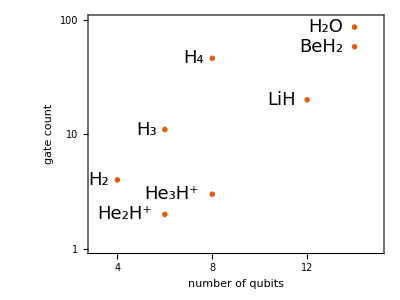

```mathematica
ListLogPlot[{gatesgrow},Joined->{False,True},
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"number of qubits","gate count"},ImageSize->400,
Frame->True,FrameStyle->Directive[Black,24],PlotRange->{{3,15},{1,100}},PlotMarkers->"OpenMarkers",
AspectRatio->3/4,Background->White,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Range[4,14,2],Automatic}},GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/vqe-best-gates.pdf",%]
```

/home/cica/chemistry/img/vqe-best-gates.pdf

```mathematica
runsum=<|#->summary[#,data]&/@Keys@hamiltonians|>;
```

Gate count: doubles, singles

```mathematica
Print@Grid[Table[{k,ToString@CountGates[bestresfin[k][[1]]]},{k,molecules}]]
```

H2 | {3, 1}
He2H | {1, 1}
He3H | {1, 2}
H3 | {8, 3}
LiH | {12, 8}
H4 | {36, 10}
H2O | {49, 37}
BeH2 | {39, 19}

Percentage of success

```mathematica
percentsucc=<|Table[k->ToString[IntegerPart[N[(succres[k]//Length),2]*10]]<>"%",{k,molecules}]|>
```

<|H2→100%,He2H→100%,He3H→100%,H3→100%,LiH→50%,H4→60%,H2O→30%,BeH2→80%|>

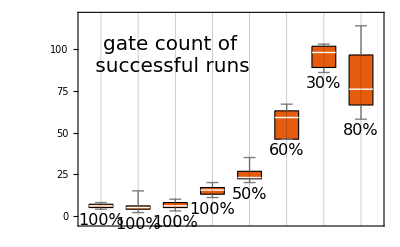

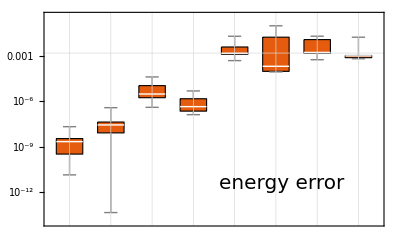

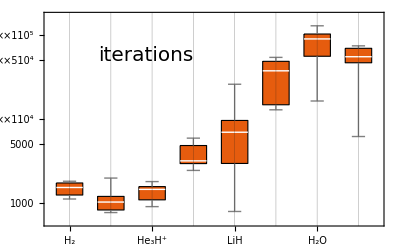

```mathematica
plotngates=BoxWhiskerChart[Values@Table[k->Select[runsum[k],#["ϵ"]<=chemacc&][[All,"ngates"]],{k,molecules}],FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],GridLines->{Range[Length@molecules],None},PlotTheme->"Scientific",GridLinesStyle->GrayLevel[0.1,0.3],Epilog->Text[Style["gate count of\n successful runs",20,FontFamily->"FreeSerif",Background->White],Scaled[{.3,.8}]],ImageSize->400,
ImagePadding->{{60,10},{0,10}},ChartLabels->Placed[Table[percentsucc[m],{m,molecules}],Below],LabelStyle->Directive[Black,16, FontFamily->"FreeSerif"]
]

plotacc=BoxWhiskerChart[Values@Table[k->runsum[k][[All,"ϵ"]],{k,molecules}],ScalingFunctions->"Log10",FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],GridLines->{Range[Length@molecules],{Log10@chemacc}},GridLinesStyle->{GrayLevel[0.1,0.3], Directive[Red,Thick ,Dashed]},PlotTheme->"Scientific",Epilog->Text[Style["energy error",20,FontFamily->"FreeSerif",Background->White],Scaled[{.7,.2}]],ImageSize->400,
ImagePadding->{{60,10},{0,0}}
]

plotfev=BoxWhiskerChart[Values@Table[k->runsum[k][[All,"nfev"]],{k,molecules}],ScalingFunctions->"Log10",FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[Table[labels[m],{m,molecules}],Axis,Rotate[#,30Degree]&],GridLines->{Range[Length@molecules],None},PlotTheme->"Scientific",GridLinesStyle->GrayLevel[0.1,0.3],Epilog->Text[Style["iterations",20,FontFamily->"FreeSerif",Background->White],Scaled[{.3,.8}]],ImageSize->400,
ImagePadding->{{60,10},{44,0}}
]
```

```mathematica
whiskers=Column[{plotngates,plotacc,plotfev},Spacings->-0.1];
```

```mathematica
Export["/home/cica/chemistry/img/whiskers.pdf",whiskers]
```

/home/cica/chemistry/img/whiskers.pdf

Best results

### Rounding the results: module ?roundingAnsatzIterate

```mathematica
succres=<| Table[mol->GetSuccData[mol] ,{mol,Keys@hamiltonians}]|>;
```

```mathematica
ClearAll[roundingAnsatzIterate]
roundingAnsatzIterate::usage="roundingAnsatzIterate[ansatz,θvars,ansatzinit,hamiltonian,ψ,ψwork,accuracy,maxfrac]. Iterate the rounding to π/j, where j is increased up to maxfrac. Iteration stops when energy difference is less than the accuracy.";
roundingAnsatzIterate[ansatz_,θvars_,ansatzinit_,hamiltonian_,ψ_,ψwork_,accuracy_,maxfrac_]:=Module[
{idx=0,newkeys,ansatznew,θvarsnew,frac,newcost,cost}
,
newkeys=Table[k->Subscript[θ, idx++],{k,Keys@θvars}];
ansatznew=ansatz/.newkeys;
frac=1;
While[frac<= maxfrac,
θvarsnew=<|Table[  (k/.newkeys)->Round[θvars[k] ,π/frac] ,{k,Keys@θvars}] |>;
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,ansatznew]/.θvarsnew];
newcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
If[(newcost-cost)<=accuracy,Break[]];
frac++;
];
{ansatznew/.θvarsnew,newcost}
]
```

```mathematica
bestres=<|Table[
mol->succres[mol][[First@Ordering[Length[#[[1]]]&/@succres[mol],1]]],{mol,Keys@hamiltonians}]|>;
```

maxfrac=200;
accuracy=10^-4;
roundRes=Table[
molecule->
With[{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[X_i,{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
result=bestres[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
{ansatz,newcost}=roundingAnsatzIterate[result[[1]],result[[2]],ansatzinit,hamiltonian,ψ,ψwork,accuracy,maxfrac];
Print["Best result of ",molecule," has ϵ=",newcost-groundstate];
{ansatz,newcost,newcost-groundstate,Length@ansatz}
],{molecule,Keys@hamiltonians}];

Best result of BeH2 has ϵ=0.00131873

Best result of LiH has ϵ=0.00151079

Best result of H2O has ϵ=0.00179457

Best result of H2 has ϵ=0.0000129511

Best result of H3 has ϵ=0.0000123006

Best result of H4 has ϵ=0.000192186

Best result of He2H has ϵ=1.23311×10^-6

Best result of He3H has ϵ=0.0000447107

roundRes = <|roundRes|>;

DumpSave["roundRes.mx", roundRes];

```mathematica
roundRes<<"roundRes.mx"
```

<|BeH2→{{Null Rx_7[(7 π)/200],Null Ry_11[(103 π)/200],Null Rx_2[(13 π)/200],Null C_7[Ry_6[π]],Null C_2[Ry_10[π]],Null Ry_10[-π],Null C_10[Ry_12[π]],Null C_10[Rx_4[π]],Null C_10[Rx_3[π]],Null C_3[Rx_10[-(33 π)/20]],Null Rx_10[(41 π)/25],Null C_10[Rz_11[(97 π)/100]],Null C_11[Rx_13[(3 π)/40]],Null C_1[Ry_11[-(147 π)/100]],Null C_11[Rx_10[-(9 π)/200]],Null Ry_11[(193 π)/200],Null C_6[Rx_10[π/20]],Null C_10[Rx_13[-(119 π)/50]],Null C_11[Rx_12[-π]],Null C_10[Rx_2[-π]],Null C_11[Ry_5[-π]],Null C_1[Rz_13[(113 π)/200]],Null C_10[Rx_9[-π/40]],Null C_12[Ry_13[-(17 π)/50]],Null Rx_11[π/2],Null Rz_5[-(23 π)/40],Null C_1[Rz_13[-(113 π)/200]],Null Rx_9[(7 π)/200],Null C_2[Rx_11[-π]],Null C_10[Ry_3[π]],Null Rx_13[-(7 π)/200],Null C_2[Rz_12[(79 π)/100]],Null Rz_11[-π/2],Null C_0[Ry_10[-(37 π)/50]],Null C_6[Rx_3[π]],Null C_5[Rz_1[-π]],Null C_7[Rx_9[-(7 π)/200]],Null C_12[Rx_2[-π]],Null C_1[Ry_10[(37 π)/50]],Null C_13[Rz_11[-π]],Null C_9[Rx_3[π]],Null C_7[Rz_8[(4 π)/5]],Null Ry_11[-π/2],Null C_10[Rz_6[(59 π)/100]],Null C_13[Ry_2[-π]],Null C_7[Rz_5[(19 π)/50]],Null C_13[Ry_4[π]],Null Rz_2[(49 π)/200],Null C_5[Rz_10[-(17 π)/20]],Null C_4[Rz_12[(21 π)/40]],Null C_9[Ry_2[-π]],Null C_5[Rz_3[-(21 π)/100]],Null C_10[Rz_13[(14 π)/25]],Null C_9[Ry_8[π]],Null C_7[Ry_2[-π]],Null C_12[Rz_6[(63 π)/100]],Null C_11[Rz_10[(23 π)/200]],Null Rz_9[-(21 π)/100]},-15.5939 Null,0.00131873 Null,58 Null},LiH→{{Null Ry_4[-(27 π)/200],Null Ry_5[(2 π)/25],Null C_5[Rx_11[π]],Null C_4[Rz_5[π]],Null C_11[Rz_7[-(141 π)/200]],Null C_5[Ry_10[(24 π)/25]],Null C_5[Rx_3[π/40]],Null C_1[Rz_10[(16 π)/25]],Null Rx_5[π],Null Rx_3[-π/40],Null C_2[Rx_10[-(9 π)/200]],Null C_3[Rx_4[-(31 π)/100]],Null C_10[Rx_2[-π]],Null Rx_4[(9 π)/20],Null Ry_3[π],Null C_2[Rz_0[(197 π)/200]],Null C_2[Ry_3[-π]],Null C_3[Rx_5[-π]],Null C_5[Rx_4[-(8 π)/25]],Null C_4[Rx_10[π]]},-7.88055 Null,0.00151079 Null,20 Null},H2O→{{Null Ry_11[(3 π)/2],Null C_5[Ry_6[-π/25]],Null C_9[Ry_3[-π/40]],Null C_2[Rx_6[-π/25]],Null C_3[Rx_12[(89 π)/100]],Null C_11[Ry_12[-(199 π)/200]],Null C_3[Rx_4[-(11 π)/100]],Null C_6[Rz_11[(103 π)/200]],Null C_4[Rx_12[-(29 π)/200]],Null C_12[Ry_11[(119 π)/100]],Null C_0[Ry_4[(19 π)/20]],Null Rx_4[(23 π)/25],Null C_5[Ry_11[-(123 π)/100]],Null C_0[Rz_12[(11 π)/100]],Null C_3[Ry_12[(3 π)/8]],Null C_11[Ry_3[(49 π)/50]],Null C_12[Rz_11[(14 π)/25]],Null C_5[Rx_3[-(51 π)/50]],Null Rx_12[(13 π)/40],Null C_3[Rx_2[π]],Null C_7[Ry_12[-(53 π)/200]],Null C_5[Rx_3[π]],Null C_12[Ry_6[(21 π)/10]],Null C_2[Ry_7[π]],Null C_1[Rx_6[(3 π)/100]],Null C_12[Rx_4[(11 π)/10]],Null C_11[Rx_2[-(193 π)/200]],Null C_0[Ry_11[π]],Null C_4[Rx_11[(13 π)/50]],Null C_0[Rx_2[-π/50]],Null C_5[Ry_4[-(11 π)/200]],Null Rx_11[(47 π)/200],Null C_11[Rz_6[-(49 π)/50]],Null C_5[Rx_12[-(43 π)/100]],Null C_3[Rx_6[(3 π)/100]],Null C_0[Ry_11[π/5]],Null C_12[Rz_13[(203 π)/100]],Null C_4[Ry_5[-π]],Null C_2[Ry_12[(79 π)/200]],Null Ry_5[π],Null C_6[Rz_7[(3 π)/4]],Null C_4[Ry_7[π]],Null C_11[Rz_12[-(3 π)/40]],Null Rx_11[(49 π)/50],Null C_12[Rz_10[(59 π)/50]],Null Rz_4[-(337 π)/200],Null C_5[Rx_10[-π]],Null C_4[Ry_11[-(61 π)/200]],Null Rx_10[-π/2],Null C_11[Rx_12[-(107 π)/200]],Null C_4[Rz_6[-(9 π)/25]],Null C_2[Rz_10[π]],Null C_11[Rx_5[π]],Null Rz_12[(17 π)/200],Null C_11[Rx_13[-π]],Null C_5[Rz_12[-(409 π)/200]],Null C_10[Rz_6[π]],Null C_5[Rz_2[-(53 π)/100]],Null C_9[Rx_10[(9 π)/20]],Null C_11[Rz_13[(77 π)/50]],Null C_2[Rz_1[-(243 π)/200]],Null Rz_5[(217 π)/200],Null C_3[Rx_10[-(57 π)/100]],Null C_4[Ry_11[-(199 π)/200]],Null C_8[Rx_5[π/2]],Null Ry_10[π/2],Null C_4[Rz_7[(193 π)/200]],Null C_3[Rz_11[(14 π)/25]],Null C_8[Ry_12[(19 π)/40]],Null Rz_10[-(147 π)/100],Null C_1[Rz_11[(87 π)/100]],Null C_7[Rz_6[-(73 π)/100]],Null C_12[Ry_13[-π]],Null Ry_11[π/2],Null C_5[Rz_12[-π]],Null C_0[Rz_13[-(361 π)/200]],Null C_8[Rz_12[-(13 π)/5]],Null C_0[Ry_5[-π/2]],Null C_12[Ry_4[-3 π]],Null C_6[Rz_4[(57 π)/100]],Null C_11[Rz_6[(197 π)/200]],Null C_6[Rz_13[(51 π)/100]],Null C_11[Rz_2[π]],Null Ry_11[-π/2],Null Rz_11[-(17 π)/200],Null C_11[Rx_7[-π]]},-75.0122 Null,0.00179457 Null,86 Null},H2→{{Null C_0[Rx_3[-(7 π)/100]],Null C_3[Ry_2[-π]],Null C_3[Ry_1[-π]],Null C_2[Rx_0[π]]},-1.13727 Null,0.0000129511 Null,4 Null},H3→{{Null C_2[Rx_0[(41 π)/200]],Null C_0[Ry_4[-(29 π)/200]],Null C_1[Ry_2[-π]],Null Rx_4[-π],Null C_4[Rx_2[π]],Null C_0[Ry_4[π]],Null C_4[Rx_5[-π]],Null C_5[Rx_1[-π]],Null C_1[Rx_3[-π/25]],Null C_3[Rx_1[π]],Null C_5[Rz_3[π]]},-1.41988 Null,0.0000123006 Null,11 Null},H4→{{Null C_2[Ry_6[-(319 π)/200]],Null C_1[Rx_5[-(29 π)/200]],Null C_5[Rx_0[-(139 π)/200]],Null C_5[Rx_3[-π]],Null C_0[Ry_6[-(7 π)/20]],Null C_6[Ry_0[(17 π)/25]],Null C_1[Rz_0[(18 π)/25]],Null C_5[Ry_1[π]],Null C_0[Rz_5[-(8 π)/25]],Null C_1[Rx_5[-(47 π)/200]],Null Ry_0[-π/8],Null C_5[Ry_4[π]],Null C_2[Rz_0[-(81 π)/100]],Null C_0[Ry_2[-π]],Null Rz_5[(27 π)/50],Null C_0[Ry_3[-π]],Null Ry_2[π],Null C_1[Ry_3[π]],Null C_6[Ry_0[(31 π)/200]],Null C_1[Rz_2[(79 π)/100]],Null C_3[Rx_1[(27 π)/200]],Null C_4[Rx_3[π]],Null C_5[Rx_1[-(51 π)/200]],Null C_1[Rx_2[-π]],Null C_0[Rx_4[π]],Null C_5[Rx_6[(139 π)/200]],Null C_4[Ry_6[(39 π)/40]],Null C_2[Ry_7[-π]],Null Rx_6[(47 π)/100],Null C_3[Rx_2[π]],Null C_1[Rx_4[-π]],Null C_7[Rz_3[(219 π)/100]],Null C_0[Rz_6[(351 π)/100]],Null C_5[Rx_6[(161 π)/200]],Null C_2[Ry_6[-(99 π)/200]],Null C_6[Ry_2[-π]],Null C_2[Rz_0[(131 π)/200]],Null Rz_6[(149 π)/200],Null C_4[Rz_6[-(131 π)/200]],Null C_2[Rz_4[-(41 π)/200]],Null C_6[Rx_0[π]],Null Rz_0[(36 π)/25],Null C_2[Rz_7[-(51 π)/200]],Null C_6[Rx_4[π]],Null C_0[Rz_3[(43 π)/200]],Null C_4[Rz_1[(137 π)/50]]},-1.99596 Null,0.000192186 Null,46 Null},He2H→{{Null C_3[Rx_5[-(9 π)/200]],Null C_5[Rx_1[π]]},-5.76993 Null,1.23311×10^-6 Null,2 Null},He3H→{{Null C_0[Ry_7[-(9 π)/200]],Null C_7[Rx_1[π]],Null Rz_1[π/2]},-8.57527 Null,0.0000447107 Null,3 Null}|>

------ Molecule BeH2 ϵ=0.00131873 ngates=58 ------

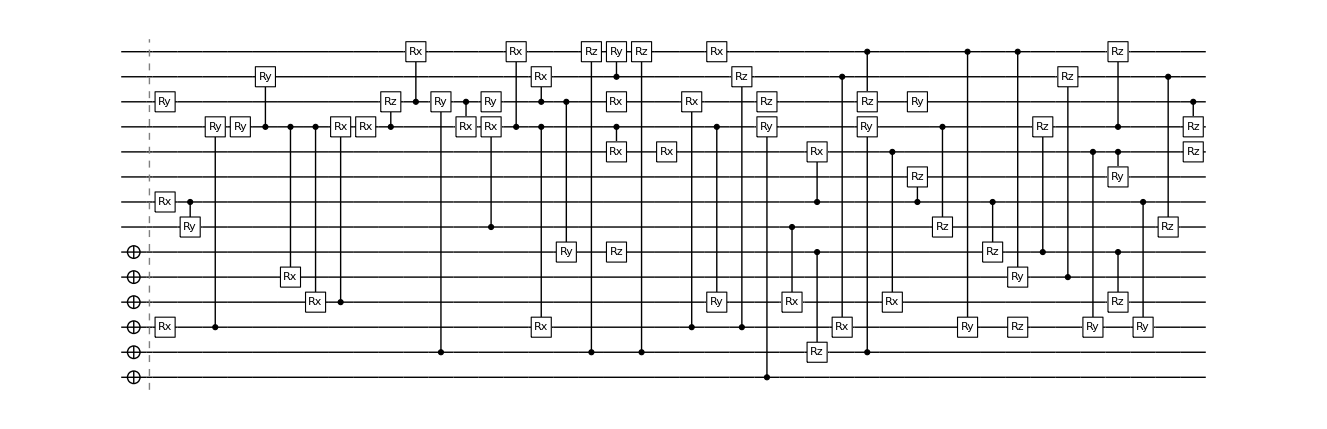

{Rx_7[(7 π)/200],Ry_11[(103 π)/200],Rx_2[(13 π)/200],C_7[Ry_6[π]],C_2[Ry_10[π]],Ry_10[-π],C_10[Ry_12[π]],C_10[Rx_4[π]],C_10[Rx_3[π]],C_3[Rx_10[-(33 π)/20]],Rx_10[(41 π)/25],C_10[Rz_11[(97 π)/100]],C_11[Rx_13[(3 π)/40]],C_1[Ry_11[-(147 π)/100]],C_11[Rx_10[-(9 π)/200]],Ry_11[(193 π)/200],C_6[Rx_10[π/20]],C_10[Rx_13[-(119 π)/50]],C_11[Rx_12[-π]],C_10[Rx_2[-π]],C_11[Ry_5[-π]],C_1[Rz_13[(113 π)/200]],C_10[Rx_9[-π/40]],C_12[Ry_13[-(17 π)/50]],Rx_11[π/2],Rz_5[-(23 π)/40],C_1[Rz_13[-(113 π)/200]],Rx_9[(7 π)/200],C_2[Rx_11[-π]],C_10[Ry_3[π]],Rx_13[-(7 π)/200],C_2[Rz_12[(79 π)/100]],Rz_11[-π/2],C_0[Ry_10[-(37 π)/50]],C_6[Rx_3[π]],C_5[Rz_1[-π]],C_7[Rx_9[-(7 π)/200]],C_12[Rx_2[-π]],C_1[Ry_10[(37 π)/50]],C_13[Rz_11[-π]],C_9[Rx_3[π]],C_7[Rz_8[(4 π)/5]],Ry_11[-π/2],C_10[Rz_6[(59 π)/100]],C_13[Ry_2[-π]],C_7[Rz_5[(19 π)/50]],C_13[Ry_4[π]],Rz_2[(49 π)/200],C_5[Rz_10[-(17 π)/20]],C_4[Rz_12[(21 π)/40]],C_9[Ry_2[-π]],C_5[Rz_3[-(21 π)/100]],C_10[Rz_13[(14 π)/25]],C_9[Ry_8[π]],C_7[Ry_2[-π]],C_12[Rz_6[(63 π)/100]],C_11[Rz_10[(23 π)/200]],Rz_9[-(21 π)/100]}

------ Molecule LiH ϵ=0.00151079 ngates=20 ------

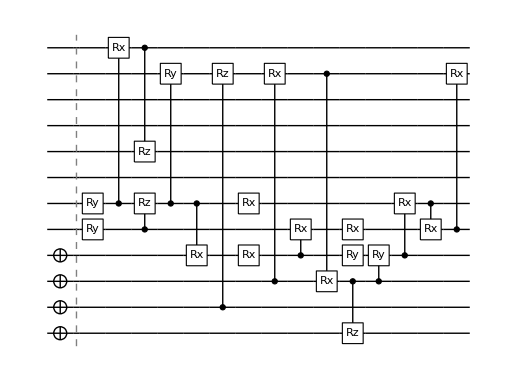

{Ry_4[-(27 π)/200],Ry_5[(2 π)/25],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-(141 π)/200]],C_5[Ry_10[(24 π)/25]],C_5[Rx_3[π/40]],C_1[Rz_10[(16 π)/25]],Rx_5[π],Rx_3[-π/40],C_2[Rx_10[-(9 π)/200]],C_3[Rx_4[-(31 π)/100]],C_10[Rx_2[-π]],Rx_4[(9 π)/20],Ry_3[π],C_2[Rz_0[(197 π)/200]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-(8 π)/25]],C_4[Rx_10[π]]}

------ Molecule H2O ϵ=0.00179457 ngates=86 ------

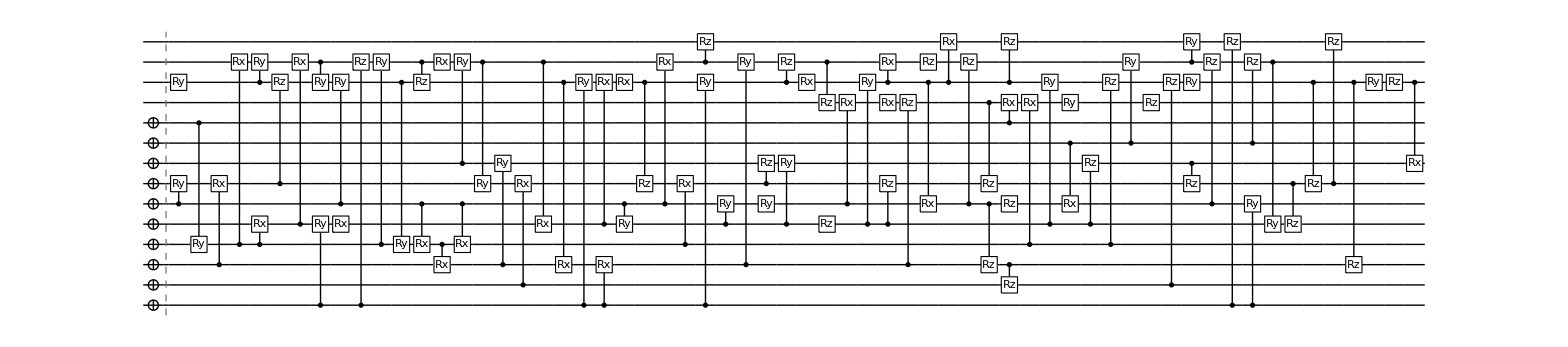

{Ry_11[(3 π)/2],C_5[Ry_6[-π/25]],C_9[Ry_3[-π/40]],C_2[Rx_6[-π/25]],C_3[Rx_12[(89 π)/100]],C_11[Ry_12[-(199 π)/200]],C_3[Rx_4[-(11 π)/100]],C_6[Rz_11[(103 π)/200]],C_4[Rx_12[-(29 π)/200]],C_12[Ry_11[(119 π)/100]],C_0[Ry_4[(19 π)/20]],Rx_4[(23 π)/25],C_5[Ry_11[-(123 π)/100]],C_0[Rz_12[(11 π)/100]],C_3[Ry_12[(3 π)/8]],C_11[Ry_3[(49 π)/50]],C_12[Rz_11[(14 π)/25]],C_5[Rx_3[-(51 π)/50]],Rx_12[(13 π)/40],C_3[Rx_2[π]],C_7[Ry_12[-(53 π)/200]],C_5[Rx_3[π]],C_12[Ry_6[(21 π)/10]],C_2[Ry_7[π]],C_1[Rx_6[(3 π)/100]],C_12[Rx_4[(11 π)/10]],C_11[Rx_2[-(193 π)/200]],C_0[Ry_11[π]],C_4[Rx_11[(13 π)/50]],C_0[Rx_2[-π/50]],C_5[Ry_4[-(11 π)/200]],Rx_11[(47 π)/200],C_11[Rz_6[-(49 π)/50]],C_5[Rx_12[-(43 π)/100]],C_3[Rx_6[(3 π)/100]],C_0[Ry_11[π/5]],C_12[Rz_13[(203 π)/100]],C_4[Ry_5[-π]],C_2[Ry_12[(79 π)/200]],Ry_5[π],C_6[Rz_7[(3 π)/4]],C_4[Ry_7[π]],C_11[Rz_12[-(3 π)/40]],Rx_11[(49 π)/50],C_12[Rz_10[(59 π)/50]],Rz_4[-(337 π)/200],C_5[Rx_10[-π]],C_4[Ry_11[-(61 π)/200]],Rx_10[-π/2],C_11[Rx_12[-(107 π)/200]],C_4[Rz_6[-(9 π)/25]],C_2[Rz_10[π]],C_11[Rx_5[π]],Rz_12[(17 π)/200],C_11[Rx_13[-π]],C_5[Rz_12[-(409 π)/200]],C_10[Rz_6[π]],C_5[Rz_2[-(53 π)/100]],C_9[Rx_10[(9 π)/20]],C_11[Rz_13[(77 π)/50]],C_2[Rz_1[-(243 π)/200]],Rz_5[(217 π)/200],C_3[Rx_10[-(57 π)/100]],C_4[Ry_11[-(199 π)/200]],C_8[Rx_5[π/2]],Ry_10[π/2],C_4[Rz_7[(193 π)/200]],C_3[Rz_11[(14 π)/25]],C_8[Ry_12[(19 π)/40]],Rz_10[-(147 π)/100],C_1[Rz_11[(87 π)/100]],C_7[Rz_6[-(73 π)/100]],C_12[Ry_13[-π]],Ry_11[π/2],C_5[Rz_12[-π]],C_0[Rz_13[-(361 π)/200]],C_8[Rz_12[-(13 π)/5]],C_0[Ry_5[-π/2]],C_12[Ry_4[-3 π]],C_6[Rz_4[(57 π)/100]],C_11[Rz_6[(197 π)/200]],C_6[Rz_13[(51 π)/100]],C_11[Rz_2[π]],Ry_11[-π/2],Rz_11[-(17 π)/200],C_11[Rx_7[-π]]}

------ Molecule H2 ϵ=0.0000129511 ngates=4 ------

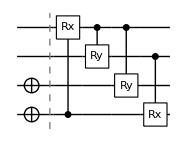

{C_0[Rx_3[-(7 π)/100]],C_3[Ry_2[-π]],C_3[Ry_1[-π]],C_2[Rx_0[π]]}

------ Molecule H3 ϵ=0.0000123006 ngates=11 ------

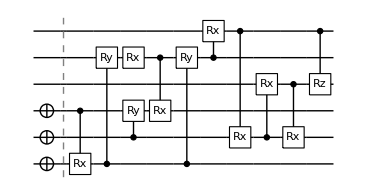

{C_2[Rx_0[(41 π)/200]],C_0[Ry_4[-(29 π)/200]],C_1[Ry_2[-π]],Rx_4[-π],C_4[Rx_2[π]],C_0[Ry_4[π]],C_4[Rx_5[-π]],C_5[Rx_1[-π]],C_1[Rx_3[-π/25]],C_3[Rx_1[π]],C_5[Rz_3[π]]}

------ Molecule H4 ϵ=0.000192186 ngates=46 ------

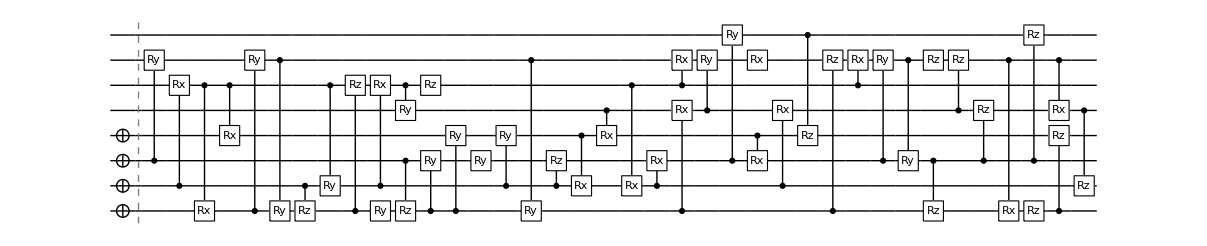

{C_2[Ry_6[-(319 π)/200]],C_1[Rx_5[-(29 π)/200]],C_5[Rx_0[-(139 π)/200]],C_5[Rx_3[-π]],C_0[Ry_6[-(7 π)/20]],C_6[Ry_0[(17 π)/25]],C_1[Rz_0[(18 π)/25]],C_5[Ry_1[π]],C_0[Rz_5[-(8 π)/25]],C_1[Rx_5[-(47 π)/200]],Ry_0[-π/8],C_5[Ry_4[π]],C_2[Rz_0[-(81 π)/100]],C_0[Ry_2[-π]],Rz_5[(27 π)/50],C_0[Ry_3[-π]],Ry_2[π],C_1[Ry_3[π]],C_6[Ry_0[(31 π)/200]],C_1[Rz_2[(79 π)/100]],C_3[Rx_1[(27 π)/200]],C_4[Rx_3[π]],C_5[Rx_1[-(51 π)/200]],C_1[Rx_2[-π]],C_0[Rx_4[π]],C_5[Rx_6[(139 π)/200]],C_4[Ry_6[(39 π)/40]],C_2[Ry_7[-π]],Rx_6[(47 π)/100],C_3[Rx_2[π]],C_1[Rx_4[-π]],C_7[Rz_3[(219 π)/100]],C_0[Rz_6[(351 π)/100]],C_5[Rx_6[(161 π)/200]],C_2[Ry_6[-(99 π)/200]],C_6[Ry_2[-π]],C_2[Rz_0[(131 π)/200]],Rz_6[(149 π)/200],C_4[Rz_6[-(131 π)/200]],C_2[Rz_4[-(41 π)/200]],C_6[Rx_0[π]],Rz_0[(36 π)/25],C_2[Rz_7[-(51 π)/200]],C_6[Rx_4[π]],C_0[Rz_3[(43 π)/200]],C_4[Rz_1[(137 π)/50]]}

------ Molecule He2H ϵ=1.23311×10^-6 ngates=2 ------

-Graphics-

{C_3[Rx_5[-(9 π)/200]],C_5[Rx_1[π]]}

------ Molecule He3H ϵ=0.0000447107 ngates=3 ------

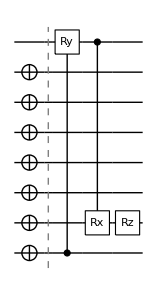

{C_0[Ry_7[-(9 π)/200]],C_7[Rx_1[π]],Rz_1[π/2]}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
Print["------ Molecule ",k," ϵ=",roundRes[k][[3]]," ngates=",Length@roundRes[k][[1]]," ------"];
Print[DrawCircuit[{Subscript[X, #]&/@Range[0,occupations[k]-1],roundRes[k][[1]]}]];
Print[roundRes[k][[1]]];
,{k,Keys@hamiltonians}]
```

### Rounding θ, if possible: roundSoftRes

```mathematica
ClearAll[roundingAnsatzSoft]
roundingAsatzSoft::usage="roundingAnsatzSoft[ansatz,θvars,ansatzinit,hamiltonian,ψ,ψwork,fraction_of_π,decimal,θerr]. Rounding to multiplication of fraction if rounding difference is less than θerr, otherwise rounded to dec decimals.";
roundingAnsatzSoft[ansatz_,θvars_,ansatzinit_,hamiltonian_,ψ_,ψwork_,fraction_,decimal_,θerr_]:=Module[
{idx=0,newkeys,ansatznew,θvarsnew,newcost,cost,roundθ}
,
newkeys=Table[k->Subscript[θ, idx++],{k,Keys@θvars}];
ansatznew=ansatz/.newkeys;

θvarsnew=<|Table[  
roundθ=Round[θvars[k] ,π/fraction] ;
(k/.newkeys)->If[Abs[roundθ-θvars[k]]<=θerr,roundθ,Round[θvars[k],N[1.0*10^-decimal]]] 
,{k,Keys@θvars}] 
|>;
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,ansatznew]/.θvarsnew];
newcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];

{ansatznew/.θvarsnew,newcost}
]
```

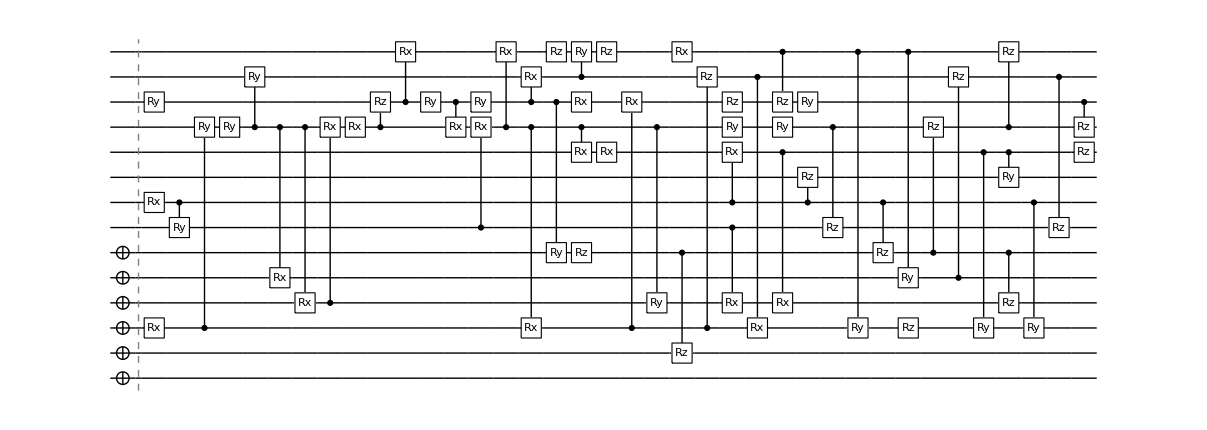
Best result of BeH2 has ϵ_new=0.0010788381843838124, ϵ_before=0.0010787209879961068
-Graphics-
{Rx_7[0.1039],Ry_11[1.6105],Rx_2[0.2116],C_7[Ry_6[π]],C_2[Ry_10[π]],Ry_10[-π],C_10[Ry_12[π]],C_10[Rx_4[π]],C_10[Rx_3[π]],C_3[Rx_10[-5.1765]],Rx_10[5.1599],C_10[Rz_11[3.055]],C_11[Rx_13[0.2289]],Ry_11[-4.6179],C_11[Rx_10[-0.147]],Ry_11[3.0383],C_6[Rx_10[0.1529]],C_10[Rx_13[-7.4751]],C_11[Rx_12[-π]],C_10[Rx_2[-π]],C_11[Ry_5[-π]],Rz_13[1.7764],C_10[Rx_9[-0.0783]],C_12[Ry_13[-1.0694]],Rx_11[π/2],Rz_5[-1.8092],Rz_13[-1.7789],Rx_9[0.1043],C_2[Rx_11[-π]],C_10[Ry_3[π]],Rx_13[-0.1172],C_2[Rz_12[2.4782]],Rz_11[-π/2],Ry_10[-2.3237],C_6[Rx_3[π]],C_5[Rz_1[-π]],C_7[Rx_9[-0.1042]],C_12[Rx_2[-π]],Ry_10[2.3237],C_13[Rz_11[-π]],C_9[Rx_3[π]],C_7[Rz_8[2.5124]],Ry_11[-π/2],C_10[Rz_6[1.8582]],C_13[Ry_2[-π]],C_7[Rz_5[1.1862]],C_13[Ry_4[π]],Rz_2[0.7628],C_5[Rz_10[-2.669]],C_4[Rz_12[1.6493]],C_9[Ry_2[-π]],C_5[Rz_3[-0.6641]],C_10[Rz_13[1.7635]],C_9[Ry_8[π]],C_7[Ry_2[-π]],C_12[Rz_6[1.9843]],C_11[Rz_10[0.3685]],Rz_9[-0.6612]}

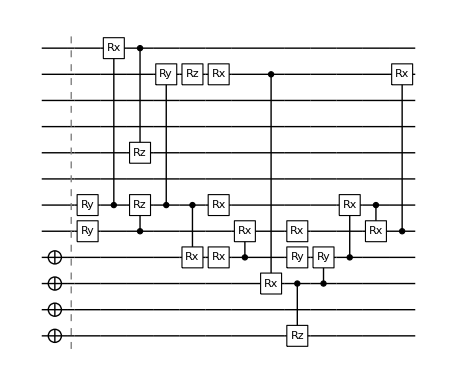
Best result of LiH has ϵ_new=0.0014428032102280497, ϵ_before=0.0014426249126735513
-Graphics-
{Ry_4[-0.4276],Ry_5[0.2591],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-2.2099]],C_5[Ry_10[3.0133]],C_5[Rx_3[0.0751]],Rz_10[2.0143],Rx_5[π],Rx_3[-0.0733],Rx_10[-0.1415],C_3[Rx_4[-0.9803]],C_10[Rx_2[-π]],Rx_4[1.4078],Ry_3[π],C_2[Rz_0[3.0974]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-1.004]],C_4[Rx_10[π]]}

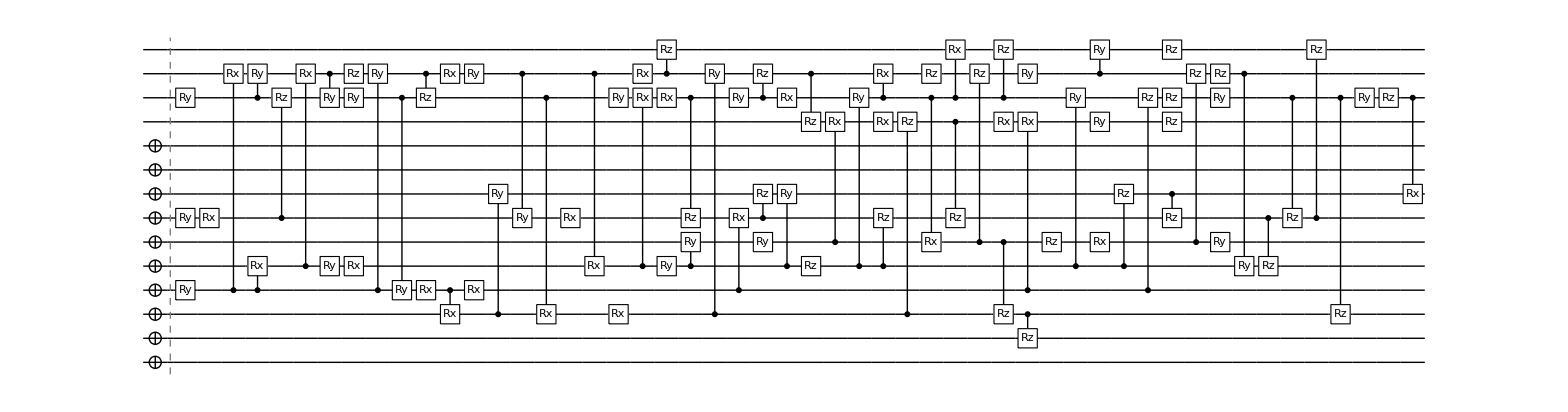
Best result of H2O has ϵ_new=0.0015490736944485661, ϵ_before=0.0015334962046864575
-Graphics-
{Ry_11[(3 π)/2],Ry_6[-0.1292],Ry_3[-0.0853],Rx_6[-0.1261],C_3[Rx_12[2.7942]],C_11[Ry_12[-3.1314]],C_3[Rx_4[-0.3406]],C_6[Rz_11[1.6156]],C_4[Rx_12[-0.4538]],C_12[Ry_11[3.7359]],Ry_4[2.9881],Rx_4[2.8956],Ry_11[-3.8586],Rz_12[0.3496],C_3[Ry_12[1.1733]],C_11[Ry_3[3.0712]],C_12[Rz_11[1.7552]],Rx_3[-3.2019],Rx_12[1.025],C_3[Rx_2[π]],Ry_12[-0.8295],Rx_3[π],C_12[Ry_6[6.5897]],C_2[Ry_7[π]],Rx_6[0.0879],C_12[Rx_4[3.4598]],C_11[Rx_2[-3.0374]],Ry_11[π],C_4[Rx_11[0.8246]],Rx_2[-0.0661],Ry_4[-0.1678],Rx_11[0.7317],C_11[Rz_6[-3.0823]],Rx_12[-1.3524],C_3[Rx_6[0.0991]],Ry_11[0.6324],C_12[Rz_13[6.3846]],C_4[Ry_5[-π]],C_2[Ry_12[1.2406]],Ry_5[π],C_6[Rz_7[(3 π)/4]],C_4[Ry_7[π]],C_11[Rz_12[-0.2303]],Rx_11[3.0728],C_12[Rz_10[3.7021]],Rz_4[-5.2987],C_5[Rx_10[-π]],C_4[Ry_11[-0.9557]],Rx_10[-π/2],C_11[Rx_12[-1.6765]],C_4[Rz_6[-1.137]],C_2[Rz_10[π]],C_11[Rx_5[π]],Rz_12[0.261],C_11[Rx_13[-π]],C_5[Rz_12[-6.42]],C_10[Rz_6[π]],C_5[Rz_2[-1.6681]],Rx_10[1.4152],C_11[Rz_13[4.8357]],C_2[Rz_1[-3.8182]],Rz_5[3.4127],C_3[Rx_10[-1.7919]],C_4[Ry_11[-π]],Rx_5[π/2],Ry_10[π/2],C_4[Rz_7[3.0338]],C_3[Rz_11[1.7592]],Ry_12[1.4915],Rz_10[-4.6226],Rz_11[2.7386],C_7[Rz_6[-2.2863]],C_12[Ry_13[-π]],Ry_11[π/2],C_5[Rz_12[-π]],Rz_13[-5.6631],Rz_12[-8.1656],Ry_5[-π/2],C_12[Ry_4[-3 π]],C_6[Rz_4[1.7949]],C_11[Rz_6[3.0914]],C_6[Rz_13[1.6007]],C_11[Rz_2[π]],Ry_11[-π/2],Rz_11[-0.27],C_11[Rx_7[-π]]}

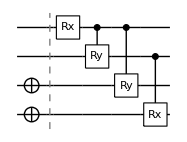
Best result of H2 has ϵ_new=4.775011497315518e-10, ϵ_before=1.361399881716352e-11
-Graphics-
{Rx_3[-0.2256],C_3[Ry_2[-π]],C_3[Ry_1[-π]],C_2[Rx_0[π]]}

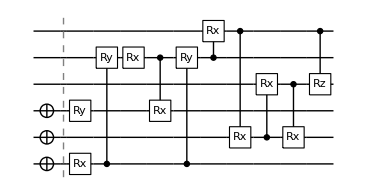
Best result of H3 has ϵ_new=2.662986460233441e-7, ϵ_before=6.60757461190542e-7
-Graphics-
{Rx_0[0.6393],C_0[Ry_4[-0.4504]],Ry_2[-π],Rx_4[-π],C_4[Rx_2[π]],C_0[Ry_4[π]],C_4[Rx_5[-π]],C_5[Rx_1[-π]],C_1[Rx_3[-0.1305]],C_3[Rx_1[π]],C_5[Rz_3[π]]}

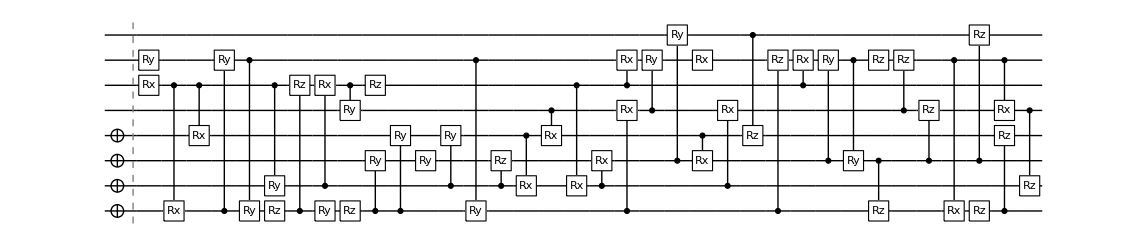
Best result of H4 has ϵ_new=0.00010731873326341734, ϵ_before=0.00010732297367055388
-Graphics-
{Ry_6[-5.0121],Rx_5[-0.4478],C_5[Rx_0[-2.1848]],C_5[Rx_3[-π]],C_0[Ry_6[-1.1047]],C_6[Ry_0[2.1436]],Rz_0[2.2614],C_5[Ry_1[π]],C_0[Rz_5[-1.0128]],C_1[Rx_5[-0.7458]],Ry_0[-0.3979],C_5[Ry_4[π]],Rz_0[-2.5433],C_0[Ry_2[-π]],Rz_5[1.6903],C_0[Ry_3[-π]],Ry_2[π],C_1[Ry_3[π]],C_6[Ry_0[0.481]],C_1[Rz_2[2.4893]],C_3[Rx_1[0.424]],C_4[Rx_3[π]],C_5[Rx_1[-0.8016]],C_1[Rx_2[-π]],C_0[Rx_4[π]],C_5[Rx_6[2.1906]],C_4[Ry_6[3.0603]],C_2[Ry_7[-π]],Rx_6[1.4797],C_3[Rx_2[π]],C_1[Rx_4[-π]],C_7[Rz_3[6.8841]],C_0[Rz_6[11.0253]],C_5[Rx_6[2.5263]],C_2[Ry_6[-1.5476]],C_6[Ry_2[-π]],C_2[Rz_0[2.0566]],Rz_6[2.3418],C_4[Rz_6[-2.0653]],C_2[Rz_4[-0.6373]],C_6[Rx_0[π]],Rz_0[4.5291],C_2[Rz_7[-0.8078]],C_6[Rx_4[π]],C_0[Rz_3[0.679]],C_4[Rz_1[8.6045]]}

Best result of He2H has ϵ_new=4.3079673162083054e-10, ϵ_before=4.3520742565306136e-14
-Graphics-
{Rx_5[-0.1435],C_5[Rx_1[π]]}

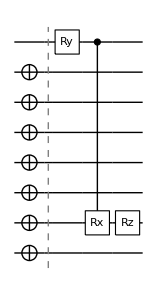
Best result of He3H has ϵ_new=0.000041722236584718075, ϵ_before=0.00004177900040502891
-Graphics-
{Ry_7[-0.1449],C_7[Rx_1[π]],Rz_1[π/2]}

```mathematica
accuracy=10^-2;
fraction=4;
decimal=4;
roundsoftRes=<|Table[
molecule->
With[{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
result=bestresfin[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,result[[1]]]/.result[[2]]];
oldcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];

{ansatz,newcost}=roundingAnsatzSoft[result[[1]],result[[2]],ansatzinit,hamiltonian,ψ,ψwork,fraction,decimal,accuracy];
Print@Column@{"Best result of "<>molecule<>" has ϵ_new="<>ToString[newcost-groundstate,FortranForm]<>", ϵ_before="<>ToString[oldcost-groundstate,FortranForm],DrawCircuit[{ansatzinit,ansatz},nqubits],ansatz};
{ansatz,newcost,newcost-groundstate,Length@ansatz}
],{molecule,Keys@hamiltonians}]|>;
```

### Print some ansatze to quantikz format

DumpSave["roundsoftRes.mx", roundsoftRes];

```mathematica
roundsoftRes<<"roundsoftRes.mx"
```

<|BeH2→{{Null Rx_7[0.1039],Null Ry_11[1.6105],Null Rx_2[0.2116],Null C_7[Ry_6[π]],Null C_2[Ry_10[π]],Null Ry_10[-π],Null C_10[Ry_12[π]],Null C_10[Rx_4[π]],Null C_10[Rx_3[π]],Null C_3[Rx_10[-5.1765]],Null Rx_10[5.1599],Null C_10[Rz_11[3.055]],Null C_11[Rx_13[0.2289]],Null Ry_11[-4.6179],Null C_11[Rx_10[-0.147]],Null Ry_11[3.0383],Null C_6[Rx_10[0.1529]],Null C_10[Rx_13[-7.4751]],Null C_11[Rx_12[-π]],Null C_10[Rx_2[-π]],Null C_11[Ry_5[-π]],Null Rz_13[1.7764],Null C_10[Rx_9[-0.0783]],Null C_12[Ry_13[-1.0694]],Null Rx_11[π/2],Null Rz_5[-1.8092],Null Rz_13[-1.7789],Null Rx_9[0.1043],Null C_2[Rx_11[-π]],Null C_10[Ry_3[π]],Null Rx_13[-0.1172],Null C_2[Rz_12[2.4782]],Null Rz_11[-π/2],Null Ry_10[-2.3237],Null C_6[Rx_3[π]],Null C_5[Rz_1[-π]],Null C_7[Rx_9[-0.1042]],Null C_12[Rx_2[-π]],Null Ry_10[2.3237],Null C_13[Rz_11[-π]],Null C_9[Rx_3[π]],Null C_7[Rz_8[2.5124]],Null Ry_11[-π/2],Null C_10[Rz_6[1.8582]],Null C_13[Ry_2[-π]],Null C_7[Rz_5[1.1862]],Null C_13[Ry_4[π]],Null Rz_2[0.7628],Null C_5[Rz_10[-2.669]],Null C_4[Rz_12[1.6493]],Null C_9[Ry_2[-π]],Null C_5[Rz_3[-0.6641]],Null C_10[Rz_13[1.7635]],Null C_9[Ry_8[π]],Null C_7[Ry_2[-π]],Null C_12[Rz_6[1.9843]],Null C_11[Rz_10[0.3685]],Null Rz_9[-0.6612]},-15.5941 Null,0.00107884 Null,58 Null},LiH→{{Null Ry_4[-0.4276],Null Ry_5[0.2591],Null C_5[Rx_11[π]],Null C_4[Rz_5[π]],Null C_11[Rz_7[-2.2099]],Null C_5[Ry_10[3.0133]],Null C_5[Rx_3[0.0751]],Null Rz_10[2.0143],Null Rx_5[π],Null Rx_3[-0.0733],Null Rx_10[-0.1415],Null C_3[Rx_4[-0.9803]],Null C_10[Rx_2[-π]],Null Rx_4[1.4078],Null Ry_3[π],Null C_2[Rz_0[3.0974]],Null C_2[Ry_3[-π]],Null C_3[Rx_5[-π]],Null C_5[Rx_4[-1.004]],Null C_4[Rx_10[π]]},-7.88062 Null,0.0014428 Null,20 Null},H2O→{{Null Ry_11[(3 π)/2],Null Ry_6[-0.1292],Null Ry_3[-0.0853],Null Rx_6[-0.1261],Null C_3[Rx_12[2.7942]],Null C_11[Ry_12[-3.1314]],Null C_3[Rx_4[-0.3406]],Null C_6[Rz_11[1.6156]],Null C_4[Rx_12[-0.4538]],Null C_12[Ry_11[3.7359]],Null Ry_4[2.9881],Null Rx_4[2.8956],Null Ry_11[-3.8586],Null Rz_12[0.3496],Null C_3[Ry_12[1.1733]],Null C_11[Ry_3[3.0712]],Null C_12[Rz_11[1.7552]],Null Rx_3[-3.2019],Null Rx_12[1.025],Null C_3[Rx_2[π]],Null Ry_12[-0.8295],Null Rx_3[π],Null C_12[Ry_6[6.5897]],Null C_2[Ry_7[π]],Null Rx_6[0.0879],Null C_12[Rx_4[3.4598]],Null C_11[Rx_2[-3.0374]],Null Ry_11[π],Null C_4[Rx_11[0.8246]],Null Rx_2[-0.0661],Null Ry_4[-0.1678],Null Rx_11[0.7317],Null C_11[Rz_6[-3.0823]],Null Rx_12[-1.3524],Null C_3[Rx_6[0.0991]],Null Ry_11[0.6324],Null C_12[Rz_13[6.3846]],Null C_4[Ry_5[-π]],Null C_2[Ry_12[1.2406]],Null Ry_5[π],Null C_6[Rz_7[(3 π)/4]],Null C_4[Ry_7[π]],Null C_11[Rz_12[-0.2303]],Null Rx_11[3.0728],Null C_12[Rz_10[3.7021]],Null Rz_4[-5.2987],Null C_5[Rx_10[-π]],Null C_4[Ry_11[-0.9557]],Null Rx_10[-π/2],Null C_11[Rx_12[-1.6765]],Null C_4[Rz_6[-1.137]],Null C_2[Rz_10[π]],Null C_11[Rx_5[π]],Null Rz_12[0.261],Null C_11[Rx_13[-π]],Null C_5[Rz_12[-6.42]],Null C_10[Rz_6[π]],Null C_5[Rz_2[-1.6681]],Null Rx_10[1.4152],Null C_11[Rz_13[4.8357]],Null C_2[Rz_1[-3.8182]],Null Rz_5[3.4127],Null C_3[Rx_10[-1.7919]],Null C_4[Ry_11[-π]],Null Rx_5[π/2],Null Ry_10[π/2],Null C_4[Rz_7[3.0338]],Null C_3[Rz_11[1.7592]],Null Ry_12[1.4915],Null Rz_10[-4.6226],Null Rz_11[2.7386],Null C_7[Rz_6[-2.2863]],Null C_12[Ry_13[-π]],Null Ry_11[π/2],Null C_5[Rz_12[-π]],Null Rz_13[-5.6631],Null Rz_12[-8.1656],Null Ry_5[-π/2],Null C_12[Ry_4[-3 π]],Null C_6[Rz_4[1.7949]],Null C_11[Rz_6[3.0914]],Null C_6[Rz_13[1.6007]],Null C_11[Rz_2[π]],Null Ry_11[-π/2],Null Rz_11[-0.27],Null C_11[Rx_7[-π]]},-75.0125 Null,0.00154907 Null,86 Null},H2→{{Null Rx_3[-0.2256],Null C_3[Ry_2[-π]],Null C_3[Ry_1[-π]],Null C_2[Rx_0[π]]},-1.13728 Null,4.77501×10^-10 Null,4 Null},H3→{{Null Rx_0[0.6393],Null C_0[Ry_4[-0.4504]],Null Ry_2[-π],Null Rx_4[-π],Null C_4[Rx_2[π]],Null C_0[Ry_4[π]],Null C_4[Rx_5[-π]],Null C_5[Rx_1[-π]],Null C_1[Rx_3[-0.1305]],Null C_3[Rx_1[π]],Null C_5[Rz_3[π]]},-1.41989 Null,2.66299×10^-7 Null,11 Null},H4→{{Null Ry_6[-5.0121],Null Rx_5[-0.4478],Null C_5[Rx_0[-2.1848]],Null C_5[Rx_3[-π]],Null C_0[Ry_6[-1.1047]],Null C_6[Ry_0[2.1436]],Null Rz_0[2.2614],Null C_5[Ry_1[π]],Null C_0[Rz_5[-1.0128]],Null C_1[Rx_5[-0.7458]],Null Ry_0[-0.3979],Null C_5[Ry_4[π]],Null Rz_0[-2.5433],Null C_0[Ry_2[-π]],Null Rz_5[1.6903],Null C_0[Ry_3[-π]],Null Ry_2[π],Null C_1[Ry_3[π]],Null C_6[Ry_0[0.481]],Null C_1[Rz_2[2.4893]],Null C_3[Rx_1[0.424]],Null C_4[Rx_3[π]],Null C_5[Rx_1[-0.8016]],Null C_1[Rx_2[-π]],Null C_0[Rx_4[π]],Null C_5[Rx_6[2.1906]],Null C_4[Ry_6[3.0603]],Null C_2[Ry_7[-π]],Null Rx_6[1.4797],Null C_3[Rx_2[π]],Null C_1[Rx_4[-π]],Null C_7[Rz_3[6.8841]],Null C_0[Rz_6[11.0253]],Null C_5[Rx_6[2.5263]],Null C_2[Ry_6[-1.5476]],Null C_6[Ry_2[-π]],Null C_2[Rz_0[2.0566]],Null Rz_6[2.3418],Null C_4[Rz_6[-2.0653]],Null C_2[Rz_4[-0.6373]],Null C_6[Rx_0[π]],Null Rz_0[4.5291],Null C_2[Rz_7[-0.8078]],Null C_6[Rx_4[π]],Null C_0[Rz_3[0.679]],Null C_4[Rz_1[8.6045]]},-1.99604 Null,0.000107319 Null,46 Null},He2H→{{Null Rx_5[-0.1435],Null C_5[Rx_1[π]]},-5.76993 Null,4.30797×10^-10 Null,2 Null},He3H→{{Null Ry_7[-0.1449],Null C_7[Rx_1[π]],Null Rz_1[π/2]},-8.57527 Null,0.0000417222 Null,3 Null}|>

```mathematica
roundsoftRes["LiH"]
```

{{Ry_4[-0.4276],Ry_5[0.2591],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-2.2099]],C_5[Ry_10[3.0133]],C_5[Rx_3[0.0751]],Rz_10[2.0143],Rx_5[π],Rx_3[-0.0733],Rx_10[-0.1415],C_3[Rx_4[-0.9803]],C_10[Rx_2[-π]],Rx_4[1.4078],Ry_3[π],C_2[Rz_0[3.0974]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-1.004]],C_4[Rx_10[π]]},-7.88062,0.0014428,20}

```mathematica
inits=Join[ConstantArray[1,4],ConstantArray[0,8]]
```

{1,1,1,1,0,0,0,0,0,0,0,0}

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/vqe/results

```mathematica
circ2quantikz[inits,roundsoftRes["LiH"][[1]],"lih.tex"]
```

circ2quantikz[{1,1,1,1,0,0,0,0,0,0,0,0},{Ry_4[-0.4276],Ry_5[0.2591],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-2.2099]],C_5[Ry_10[3.0133]],C_5[Rx_3[0.0751]],Rz_10[2.0143],Rx_5[π],Rx_3[-0.0733],Rx_10[-0.1415],C_3[Rx_4[-0.9803]],C_10[Rx_2[-π]],Rx_4[1.4078],Ry_3[π],C_2[Rz_0[3.0974]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-1.004]],C_4[Rx_10[π]]},lih.tex]

## Other people results

https://journals.aps.org/prxquantum/abstract/10.1103/PRXQuantum.2.020337
feature: fixed ansatz with permutation accounted which improves the accuracy

```mathematica
ansatz1[nq_,singles_,nlayer_]:=Table[
If[OddQ@layer,
Flatten@{Table[Subscript[s, q],{s,singles},{q,Range[0,nq-1]}],Table[Subscript[C, q-1][Subscript[X, q]],{q,Range[1,nq-1,2]}]}
,
Flatten@{Table[Subscript[s, q],{s,singles},{q,Range[1,nq-2]}],
Table[Subscript[C, i-1][Subscript[X, i]],{i,2,nq-2,2}]}
],{layer,nlayer}]
```

LiH

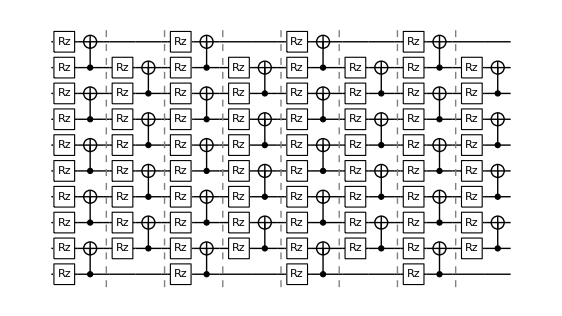

108

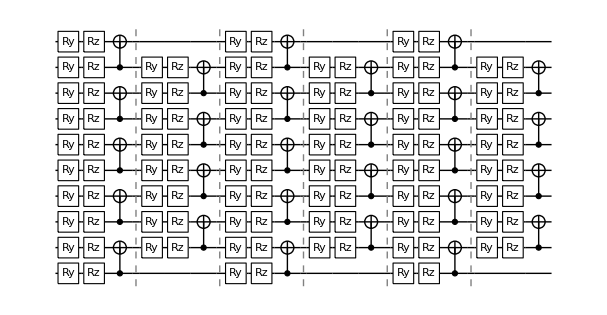

135

```mathematica
nq=10;
ansatz=ansatz1[nq,{Rz},8];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz

ansatz=ansatz1[nq,{Ry,Rz},6];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz
```

```mathematica
CountGates[Flatten@ansatz1[nq,{Rz},10]]
```

{45,90}

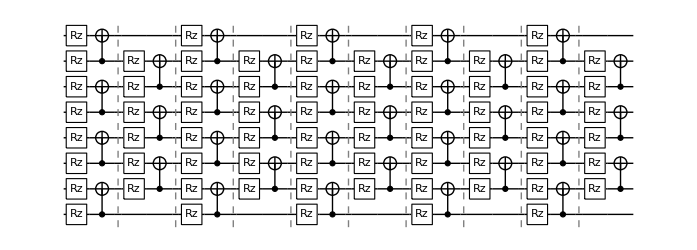

105

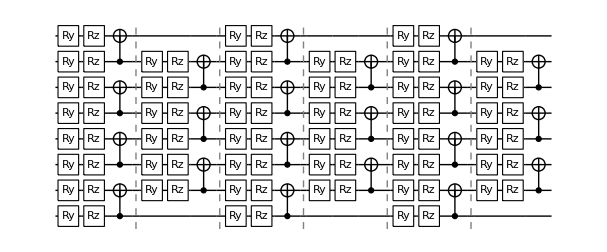

105

```mathematica
nq=8;
ansatz=ansatz1[nq,{Rz},10];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz

ansatz=ansatz1[nq,{Ry,Rz},6];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz
```

## Analysis on the hardness of the ground state: entanglement and simple results

### Reference : https://arxiv.org/pdf/2111.03132.pdf,https://arxiv.org/pdf/2107.09155.pdf

```mathematica
VonNeumann[σ_]:=-Total[#*Log2[#]&/@σ]
```

```mathematica
GSInfo::usage="GSInfo[hamiltonian], return the analysis of the ground state of a hamiltonian."
GSInfo[hamiltonian_]:=Module[{eigvecs,eigs,gsidx,C,dim,u,σ,v,scoeff,vnentropy},
{eigs,eigvecs}=Eigensystem[CalcPauliSumMatrix[hamiltonian]];
gsidx=Ordering[eigs,1]//First;

(*reshape into bipartite state, then perfom SVD*)
dim=Sqrt@Length@eigvecs[[gsidx]];
C=ArrayReshape[eigvecs[[gsidx]],{dim,dim}];
{u,σ,v}=SingularValueDecomposition[C];
(*schmidt form*)
scoeff=Select[Diagonal@σ,#>0&];
vnentropy=VonNeumann[scoeff];
<|"eigvec"->eigvecs[[gsidx]], "eigval"->eigs[[gsidx]],"svd"->{u,σ,v},"srank"->Length@scoeff,"vnentropy"->vnentropy |>
]
```

GSInfo[hamiltonian], return the analysis of the ground state of a hamiltonian.

gsinfo = <|Table[
    Print["gather info on molecule ", mol];
    mol -> GSInfo[hamiltonians[mol][[1]]], {mol, hamiltonians // Keys}]
   |>;

gather info on molecule BeH2

gather info on molecule LiH

gather info on molecule H2O

gather info on molecule H2

gather info on molecule H3

gather info on molecule H4

gather info on molecule He2H

gather info on molecule He3H

```mathematica
gsinfo<<gsinfo.mx;
```

```mathematica
Table[gsinfo[m]["vnentropy"]=VonNeumann[Select[Diagonal@gsinfo[m]["svd"][[2]],#>0&]],{m,molecules}]
```

{0.363812,0.276227,0.27742,1.28719,0.947925,3.07336,1.97236,2.00669}

```mathematica
labelpos=<|"BeH2"->Left,"LiH"->Right,"H2O"->Right,"H2"->None,"H3"->Right,"H4"->Right,"He2H"->None,"He3H"->Above|>
```

<|BeH2→Left,LiH→Right,H2O→Right,H2→None,H3→Right,H4→Right,He2H→None,He3H→Above|>

```mathematica
srank=Table[Labeled[{N@Log2[gsinfo[mol]["srank"]],Around@(Length@#&/@succres[mol][[All,1]])},labels[mol],labelpos[mol],Background->None,FrameMargins->0],{mol,molecules}]/.{"He_3H^+":>"He_3H^+\nHe_2H^+\nH_2"}
```

{Labeled[{1.,6.01.5},H_2,None,Background→None,FrameMargins→0],Labeled[{1.,6.4.},He_2H^+,None,Background→None,FrameMargins→0],Labeled[{1.,6.62.3},He_3H^+
He_2H^+
H_2,Above,Background→None,FrameMargins→0],{3.,15.42.9}H_3,{3.,25.6.}LiH,{4.,57.9.}H_4,{4.64386,96.9.}H_2O,{5.67243,81.20.}BeH_2}

```mathematica
vnentropy=Table[Labeled[{gsinfo[mol]["vnentropy"],bestres
[mol][[1]]//Length},labels[mol]],{mol,molecules}]
```

{{0.363812,4}H_2,{0.276227,2}He_2H^+,{0.27742,3}He_3H^+,{1.28719,11}H_3,{0.947925,20}LiH,{3.07336,46}H_4,{1.97236,86}H_2O,{2.00669,58}BeH_2}

```mathematica
groundstates
```

<|H2O→-75.014,LiH→-7.88206,H2→-1.13728,H4→-1.99615,He2H→-5.76993,He3H→-8.57531,BeH2→-15.5952,H3→-1.41989|>

```mathematica
sranktwo=Table[Labeled[{N@Log2[gsinfo[mol]["srank"]],Around@(CountGates[#][[1]]&/@
succresfin[mol][[All,1]])},labels[mol],labelpos[mol],Background->None,FrameMargins->0],{mol,molecules}]/.{"He_3H^+":>"H_2\nHe_2H^+\nHe_3H^+"}
```

{Labeled[{1.,3.91.2},H_2,None,Background→None,FrameMargins→0],Labeled[{1.,1.50.7},He_2H^+,None,Background→None,FrameMargins→0],Labeled[{1.,2.40.7},H_2
He_2H^+
He_3H^+,Above,Background→None,FrameMargins→0],{3.,10.31.9}H_3,{3.,16.4.}LiH,{4.,43.6.}H_4,{4.64386,61.11.}H_2O,{5.67243,50.11.}BeH_2}

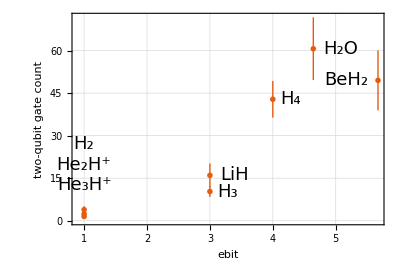

```mathematica
ListPlot[sranktwo,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"ebit","two-qubit gate count"},ImageSize->400,
Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,PlotMarkers->"OpenMarkers",
AspectRatio->2/3,Background->White,PlotTheme->"Scientific",GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/sranktwo.pdf",%]
```

/home/cica/chemistry/img/sranktwo.pdf

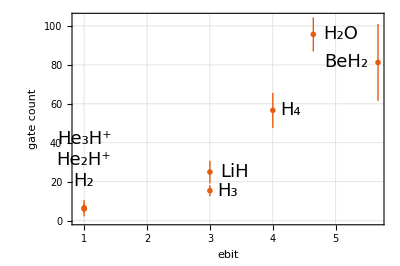

```mathematica
ListPlot[srank,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"ebit","gate count"},ImageSize->400,
Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,PlotMarkers->"OpenMarkers",
AspectRatio->2/3,Background->White,PlotTheme->"Scientific",GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/srank.pdf",%]
```

/home/cica/chemistry/img/srank.pdf

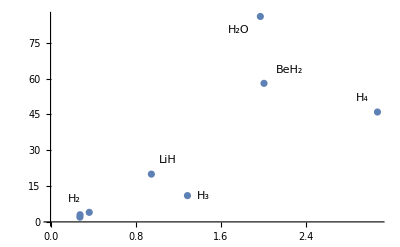

```mathematica
ListPlot[vnentropy]
```

### Simple results: He_n H^+

```mathematica
ClearAll[printstate]
```

```mathematica
printstate[vec_,mol_,printint_:False]:=Module[{vecsimp,nonzero,basis,basisint},
vecsimp=vec//Chop;
nonzero=Select[vecsimp,Abs@#>0&];
basisint=(-1+Ordering[vecsimp,-Length@nonzero]);
basis=IntegerString[#,2,hamiltonians[mol][[3]]]&/@basisint;
If[printint,
Print@Total@Table[nonzero[[i]]basisint[[i]] ,{i,Length@nonzero}]
];
Total@Table[nonzero[[i]]basis[[i]] ,{i,Length@nonzero}] 
]
```

```mathematica
resandgs::usage="resandgs[ansatz,mol]. Compare result to the ground state"
resandgs[ansatz_,mol_]:=Module[{einit,vec,efin,ψ,ψwork},
(*result*)
Print["result"];
Print@DrawCircuit[{initcirc[mol],ansatz}];
{ψ,ψwork}=CreateQuregs[hamiltonians[mol][[-1]],2];
ApplyCircuit[ψ,initcirc[mol]];
einit=CalcExpecPauliSum[ψ,hamiltonians[mol][[1]],ψwork];
vec=GetQuregMatrix[ψ]//Chop;
Print["ψ_init=",printstate[vec,mol],"  ϵ_init=",einit-groundstates[mol]];

ApplyCircuit[ψ,ansatz];
efin=CalcExpecPauliSum[ψ,hamiltonians[mol][[1]],ψwork];
vec=GetQuregMatrix[ψ]//Chop;
Print["ψ_θ=",printstate[vec,mol],"  ϵ_θ=",efin-groundstates[mol]];
(*true ground state*)
Print["ψ_gs=",printstate[gsinfo[mol]["eigvec"],mol]];
DestroyAllQuregs[];
]
```

resandgs[ansatz,mol]. Compare result to the ground state

```mathematica
roundsoftRes["He2H"][[1]]
```

{Rx_5[-0.1435],C_5[Rx_1[π]]}

```mathematica
0.071669^2+0.997428^2
```

0.999999

```mathematica
resandgs[roundsoftRes["He2H"][[1]],"He2H"]
```

result

-Graphics-

ψ_init=1. 011111  ϵ_init=0.00580407

ψ_θ=0.0716885 011111+0.997427 111101  ϵ_θ=4.30797×10^-10

ψ_gs=0.071669 011111+0.997428 111101

```mathematica
mol="He3H";
ansatz=bestresfin[mol][[1]]/.bestresfin[mol][[2]]
resandgs[ansatz,mol]
```

{Ry_7[-0.144889],C_7[Rx_1[3.14683]],Rz_1[1.57321]}

result

-Graphics-

ψ_init=1. 01111111  ϵ_init=0.00596031

ψ_θ=(0.000133789+0.000134112 ⅈ) 01111111+(0.0512429+0.0511194 ⅈ) 11111101+(0.704401+0.706103 ⅈ) 11111111  ϵ_θ=0.000041779

ψ_gs=0.0721544 10111111+0.997377 11101111+0.005658 11111110

```mathematica
ansatz=roundsoftRes["H2"][[1]]
resandgs[ansatz,"H2"]
```

{Rx_3[-0.2256],C_3[Ry_2[-π]],C_3[Ry_1[-π]],C_2[Rx_0[π]]}

result

-Graphics-

ψ_init=1. 0011  ϵ_init=0.0205245

ψ_θ=-0.112561 0011+0.993645 1111  ϵ_θ=4.77501×10^-10

ψ_gs=0.112544 1100-0.993647 1111

```mathematica
{eigvalsh2,eigstatesh2}=Eigensystem[CalcPauliSumMatrix[hamiltonians["H2"][[1]]]];
```

```mathematica
Ordering[eigvalsh2]
```

{1,4,5,6,7,8,10,11,16,15,14,12,13,9,3,2}

```mathematica
printstate[eigstatesh2[[7]],"H2"]
```

0.707107 0110+0.707107 1001

```mathematica
{eigvals,eigstates}=Eigensystem[CalcPauliSumMatrix[hamiltonians[mol][[1]]]];
```

```mathematica
eigvals=eigvals//Chop;
```

```mathematica
(0.00013378912144430087+0.00013411239311187558 ⅈ) "01111111"+(0.05124290432588843+0.05111938569536946 ⅈ) "11111101"+(0.7044005332644836+0.7061025605486954 ⅈ) "11111111"
```

(0.000133789+0.000134112 ⅈ) 01111111+(0.0512429+0.0511194 ⅈ) 11111101+(0.704401+0.706103 ⅈ) 11111111

```mathematica
eigvals[[;;8]]-groundstates[mol]
```

{1.77636×10^-15,3.55271×10^-15,0.0746111,0.670735,0.836941,0.836941,0.836941,0.872284}

```mathematica
TableForm[{printstate[#,mol]}&/@eigstates[[;;8]]]
```

0.0721544 10111111+0.997377 11101111+0.005658 11111110
-0.997377 11111100-0.005658 11111110-0.0721544 11111111
-0.047192 00111111+0.00131044 01101111-0.046797 10111101-0.00131044 11011110+0.997624 11111001+0.000946704 11111010-0.0127417 11111011-0.000946704 11111101+0.0127417 11111110-0.000584767 11111111
1. 11111111
-0.000641025 01110111-0.000641025 01111011+0.000161419 10110111+0.00334976 11010111-0.000226089 11011011-0.000843516 11100111+0.00334976 11111010+0.238449 11111011+0.676067 11111100+0.676067 11111101-0.170243 11111110+0.00118146 11111111
0.0000168662 01110111-0.000723586 10111011-0.000612254 11010111+0.0000168662 11101011-0.0000881363 11110110+0.645723 11111000+0.00378119 11111001-0.0177882 11111011-0.0177882 11111100+0.763141 11111101+0.00319941 11111110-0.0000881363 11111111
-0.000195709 01111011-0.000195709 10110111-0.000591073 10111011+0.00308872 11011011+0.0010227 11100111+0.000687771 11101011+0.0010227 11110101-0.725368 11111011+0.206407 11111100+0.206407 11111101+0.623384 11111110-0.00359403 11111111
-0.000182984 01011111-1.23559×10^-6 01101111-0.0626401 10011111-1.23559×10^-6 10101111+0.986119 11111000+0.0000194515 11111001-0.153743 11111010-3.03261×10^-6 11111011+0.0000194515 11111100+0.00288064 11111101-3.03261×10^-6 11111110-0.000449112 11111111

```mathematica
mol="H2O";
ansatz=roundsoftRes[mol][[1]]
resandgs[ansatz,mol]
```

{Ry_11[(3 π)/2],Ry_6[-0.1292],Ry_3[-0.0853],Rx_6[-0.1261],C_3[Rx_12[2.7942]],C_11[Ry_12[-3.1314]],C_3[Rx_4[-0.3406]],C_6[Rz_11[1.6156]],C_4[Rx_12[-0.4538]],C_12[Ry_11[3.7359]],Ry_4[2.9881],Rx_4[2.8956],Ry_11[-3.8586],Rz_12[0.3496],C_3[Ry_12[1.1733]],C_11[Ry_3[3.0712]],C_12[Rz_11[1.7552]],Rx_3[-3.2019],Rx_12[1.025],C_3[Rx_2[π]],Ry_12[-0.8295],Rx_3[π],C_12[Ry_6[6.5897]],C_2[Ry_7[π]],Rx_6[0.0879],C_12[Rx_4[3.4598]],C_11[Rx_2[-3.0374]],Ry_11[π],C_4[Rx_11[0.8246]],Rx_2[-0.0661],Ry_4[-0.1678],Rx_11[0.7317],C_11[Rz_6[-3.0823]],Rx_12[-1.3524],C_3[Rx_6[0.0991]],Ry_11[0.6324],C_12[Rz_13[6.3846]],C_4[Ry_5[-π]],C_2[Ry_12[1.2406]],Ry_5[π],C_6[Rz_7[(3 π)/4]],C_4[Ry_7[π]],C_11[Rz_12[-0.2303]],Rx_11[3.0728],C_12[Rz_10[3.7021]],Rz_4[-5.2987],C_5[Rx_10[-π]],C_4[Ry_11[-0.9557]],Rx_10[-π/2],C_11[Rx_12[-1.6765]],C_4[Rz_6[-1.137]],C_2[Rz_10[π]],C_11[Rx_5[π]],Rz_12[0.261],C_11[Rx_13[-π]],C_5[Rz_12[-6.42]],C_10[Rz_6[π]],C_5[Rz_2[-1.6681]],Rx_10[1.4152],C_11[Rz_13[4.8357]],C_2[Rz_1[-3.8182]],Rz_5[3.4127],C_3[Rx_10[-1.7919]],C_4[Ry_11[-π]],Rx_5[π/2],Ry_10[π/2],C_4[Rz_7[3.0338]],C_3[Rz_11[1.7592]],Ry_12[1.4915],Rz_10[-4.6226],Rz_11[2.7386],C_7[Rz_6[-2.2863]],C_12[Ry_13[-π]],Ry_11[π/2],C_5[Rz_12[-π]],Rz_13[-5.6631],Rz_12[-8.1656],Ry_5[-π/2],C_12[Ry_4[-3 π]],C_6[Rz_4[1.7949]],C_11[Rz_6[3.0914]],C_6[Rz_13[1.6007]],C_11[Rz_2[π]],Ry_11[-π/2],Rz_11[-0.27],C_11[Rx_7[-π]]}

result

-Graphics-

ψ_init=1. 00001111111111  ϵ_init=0.050225

ψ_θ=(0.0000427296+0.0000513001 ⅈ) 00001110000111-(0.000831545+0.0000348969 ⅈ) 00001111111111+(1.67555×10^-6-5.47436×10^-6 ⅈ) 00011100001011-(0.0344526+0.0243731 ⅈ) 00011101001111+(7.35297×10^-7+2.61466×10^-6 ⅈ) 00011101110011-(0.0375306+0.0269243 ⅈ) 00011111000111+(0.000209458+0.000245564 ⅈ) 00101100111011+(0.0015104+0.00122438 ⅈ) 00101101111111-(0.0000921965+0.000149208 ⅈ) 00101110001111+(7.1335×10^-7-7.62306×10^-6 ⅈ) 00101110110011+(0.00365894+0.00311274 ⅈ) 00111101111011+(0.0000409566-0.000162937 ⅈ) 00111110001011+(0.000407519+0.000148589 ⅈ) 01001100011111-(9.5379×10^-6-1.38277×10^-6 ⅈ) 01001100100011-(2.76509×10^-6-0.0000103208 ⅈ) 01001101100111+(0.000346454-0.000134997 ⅈ) 01001110010111+(8.96208×10^-7+0.000216439 ⅈ) 01001111010011-(0.00110516+0.0000173709 ⅈ) 01001111101111-(0.0000165911+2.48709×10^-6 ⅈ) 01011100011011-(0.000377125+0.000132105 ⅈ) 01011100100111+(9.94006×10^-6+3.20537×10^-6 ⅈ) 01011110010011-(0.0000134241-3.48906×10^-6 ⅈ) 01011110101111-(0.000107245+0.000600626 ⅈ) 01011111010111+(3.07224×10^-6-9.41382×10^-7 ⅈ) 01011111101011-(0.0127825+0.00947194 ⅈ) 01101100010111-(0.00132709-0.000161639 ⅈ) 01101110011111+(0.0000141689+0.0000198635 ⅈ) 01101110100011+(0.000397554-0.00121669 ⅈ) 01101111011011-(5.71231×10^-6+0.0000107214 ⅈ) 01111101010111+(0.000544022+0.000200007 ⅈ) 01111101101011+(0.0164787+0.0113386 ⅈ) 10001100010011-(7.77985×10^-6+0.000018152 ⅈ) 10001100101111+(0.000123026+7.07244×10^-6 ⅈ) 10001101101011-(0.0000808989+0.000102404 ⅈ) 10001110011011+(0.0000228515-0.0000106419 ⅈ) 10001110100111-(0.0639955+0.0450799 ⅈ) 10011100010111+(0.000255963-6.99771×10^-6 ⅈ) 10011100101011+(0.0000172575+9.65921×10^-6 ⅈ) 10011101010011+(0.00353471+0.0028728 ⅈ) 10011101101111-(3.35517×10^-6+2.26881×10^-6 ⅈ) 10011110100011-(0.00437211+0.0030317 ⅈ) 10011111100111-(0.00152883-0.00130304 ⅈ) 10101100011011+(0.0281398+0.0200739 ⅈ) 10101100100111+(0.00541959+0.00350754 ⅈ) 10101101011111+(0.0000538052+0.0000605611 ⅈ) 10101101100011-(0.0000166453+1.85507×10^-6 ⅈ) 10101110010011+(0.000498258+0.000179455 ⅈ) 10101111010111-(0.0000331337+0.0000465754 ⅈ) 10111100011111+(0.000237249+0.0000819745 ⅈ) 10111101100111-(0.0000113287+0.0000210128 ⅈ) 10111111010011+(0.00123896+0.000496277 ⅈ) 10111111101111+(0.0102523+0.00949977 ⅈ) 11001100000011-(3.73822×10^-6-2.79231×10^-6 ⅈ) 11001101000111+(0.00838982+0.00614523 ⅈ) 11001110001011-(8.88056×10^-6-0.0000133842 ⅈ) 11001110110111+(0.0000123247-0.000456055 ⅈ) 11011100000111+(0.000431736-0.00073388 ⅈ) 11011101111111+(0.00153071+0.000375028 ⅈ) 11011110001111-(0.0261559+0.0181619 ⅈ) 11011110110011+(0.000703135-0.000308932 ⅈ) 11011111001011-(2.0293×10^-6-0.0000170144 ⅈ) 11101110000011+(0.0000338331+0.0000498932 ⅈ) 11101110111111+(1.46422×10^-6+4.97322×10^-7 ⅈ) 11101111000111+(5.00424×10^-8+2.10769×10^-6 ⅈ) 11111100001111-(1.95383×10^-6+2.31037×10^-6 ⅈ) 11111100110011+(0.000100949+0.00021897 ⅈ) 11111101110111-(0.000186298+0.0000717703 ⅈ) 11111110000111-(0.00040323+0.0000666451 ⅈ) 11111111000010-(0.000924864+0.000331002 ⅈ) 11111111000011-(0.000266714-0.000527792 ⅈ) 11111111000100-(0.0000937566-0.000150309 ⅈ) 11111111000101-(0.00146927-0.00289735 ⅈ) 11111111000110+(0.000984596-0.000894209 ⅈ) 11111111000111-(0.000822695+0.000946441 ⅈ) 11111111001000-(0.00114357+0.000229978 ⅈ) 11111111001001+(0.807108+0.568096 ⅈ) 11111111001010+(3.59455×10^-6+1.56073×10^-6 ⅈ) 11111111001011-(0.000253994+0.000310362 ⅈ) 11111111001100+(0.000345466+0.000420736 ⅈ) 11111111001101+(0.000261421+0.000322006 ⅈ) 11111111001110-(1.50439×10^-6+4.17465×10^-6 ⅈ) 11111111001111-(0.000376697+0.000459171 ⅈ) 11111111010000+(0.0000123854+2.13696×10^-6 ⅈ) 11111111010001-(0.000254948+0.000308169 ⅈ) 11111111010010-(8.91482×10^-6-0.0000141103 ⅈ) 11111111010011+(0.0000131177+8.69274×10^-6 ⅈ) 11111111010100-(0.0000146004-1.04633×10^-6 ⅈ) 11111111010101+(0.0116628+0.00416914 ⅈ) 11111111010110+(5.09981×10^-6-5.43658×10^-7 ⅈ) 11111111010111+(1.45909×10^-6-7.27595×10^-6 ⅈ) 11111111011000-(6.30803×10^-7-2.13168×10^-6 ⅈ) 11111111011001-(8.07175×10^-6-0.000039959 ⅈ) 11111111011010-(0.000204274+0.000288644 ⅈ) 11111111011011-(0.0386909+0.0272582 ⅈ) 11111111011100-(0.000996642-0.0000991353 ⅈ) 11111111011101+(0.0261307+0.0182489 ⅈ) 11111111011110+(0.000309242+0.0000434629 ⅈ) 11111111011111-(0.0261041+0.0184376 ⅈ) 11111111100000-(0.0354754+0.0249702 ⅈ) 11111111100001-(0.0269219+0.019174 ⅈ) 11111111100010+(0.000269381+0.000334818 ⅈ) 11111111100011+(9.8447×10^-6+8.6877×10^-7 ⅈ) 11111111100100-(0.000162984+0.00019309 ⅈ) 11111111100101+(0.000244232+0.000298423 ⅈ) 11111111100110+(0.0000103961-0.0000144109 ⅈ) 11111111100111-(5.2112×10^-6-2.89384×10^-6 ⅈ) 11111111101000+(0.0000122317-2.04857×10^-6 ⅈ) 11111111101001+(0.000376027+0.000465221 ⅈ) 11111111101010+(0.000517504-0.0012636 ⅈ) 11111111101011+(0.000211677+0.00155947 ⅈ) 11111111101100-(0.000423427+0.00185462 ⅈ) 11111111101101-(0.000210827+0.00094484 ⅈ) 11111111101110+(0.000675319+0.00135473 ⅈ) 11111111101111+(0.0101796+0.00719413 ⅈ) 11111111110000+(0.0000862932-0.0000596552 ⅈ) 11111111110001+(0.00852709+0.00617182 ⅈ) 11111111110010+(0.000492126-0.00132776 ⅈ) 11111111110011-(0.000338719-0.000333018 ⅈ) 11111111110100-(0.000895874-0.000417325 ⅈ) 11111111110101-(0.0387681+0.0277372 ⅈ) 11111111110110+(0.0278056+0.0199888 ⅈ) 11111111110111+(0.000774556-0.000142531 ⅈ) 11111111111000+(0.0166217+0.0113653 ⅈ) 11111111111001-(0.0251006+0.0177282 ⅈ) 11111111111010-(0.0000127019+0.0000141239 ⅈ) 11111111111011-(0.000147194+0.0000529344 ⅈ) 11111111111100+(8.4397×10^-7-1.01032×10^-6 ⅈ) 11111111111101+(0.000123786+0.0000461016 ⅈ) 11111111111110  ϵ_θ=0.00154907

ψ_gs=0.0000233012 00001111111111+0.0000193586 00011111111110+0.00503022 00101101111111+0.00100331 00101111110111+0.0000429975 00111101111011-0.00175068 00111101111110-0.0000272722 00111111111001+0.0000647321 01001111101111-0.0000345243 01011110101111-0.0000117052 01011111101011-0.0000429975 01101110011111+0.0000117052 01101111011011+0.0000144547 01101111011110-0.0000328159 01101111101101+0.00215218 01110011101111-6.73058×10^-6 01111100101111+0.00228895 01111101101011+0.0000272722 01111110011011-0.0101784 01111110011110-0.0165158 01111111011010-0.00164048 01111111100011-0.0000179331 01111111101001+0.00164048 01111111101100+0.0000687957 10011101101111+0.000156178 10011111011110+0.00511378 10011111100111+0.0000134573 10011111101101-0.0000259012 10101101011111+0.0000345243 10101111010111-0.000156178 10111101100111+0.0000123106 10111101101101-0.0000111163 10111110010111-0.0000247763 10111111010110-0.0779366 10111111100101-0.0000647321 11001110110111+0.00144725 11001110111101-0.000341986 11001111111001+0.000012013 11010011111011-0.00370945 11010011111110-0.0000187239 11011100111011+0.0000187239 11011110001111+0.000719733 11011110110110+0.00175068 11011110111001+0.0000134573 11011111001110-0.0418776 11011111111000-7.14091×10^-6 11100001111111+0.000507905 11101100111101+0.000341986 11101101110011+7.14091×10^-6 11101101110110-0.000719733 11101101111001-0.000416197 11101101111100+0.0000193586 11101111000111-0.000012013 11101111110001+0.000743034 11110000111111-0.000507905 11110001111110+0.000019447 11110010110111+0.00965597 11110011001111+0.0000111163 11110011110011+0.000116359 11110011110110-0.0000865918 11110011111100+0.0000259012 11111100001111+0.0000162584 11111100110011+0.0000865918 11111100110110+6.73058×10^-6 11111100111100-0.00100331 11111101001110-0.0000144547 11111101110010+0.000043529 11111110000111+0.00370945 11111110110100+0.986413 11111110111110-0.0126449 11111110111111-0.00012703 11111111000000+0.0000313204 11111111000001+0.0126449 11111111000010-0.00503022 11111111000011+0.00012703 11111111000100-0.0000313204 11111111000101-0.000019447 11111111000110-0.0266694 11111111000111-0.046603 11111111001000+0.0330081 11111111001010+0.000110642 11111111001011-0.000116359 11111111001100-0.0330081 11111111001101-0.000110642 11111111001110-0.0433288 11111111001111-0.0318089 11111111010000-0.000288432 11111111010001+0.000288432 11111111010010-0.000639005 11111111010011+0.00303349 11111111010100+0.012822 11111111010101+0.0106919 11111111010110-0.000472944 11111111010111-0.0475335 11111111011000+0.0347115 11111111011001+0.0203914 11111111011010+0.000232928 11111111011011-0.0310834 11111111011100+0.000240016 11111111011101+0.00263175 11111111011110+0.000481304 11111111011111+0.0010545 11111111100000-3.82782×10^-7 11111111100001+0.0000412469 11111111100010+6.33741×10^-6 11111111100011-0.00109575 11111111100100-5.95463×10^-6 11111111100101+0.0000123106 11111111100110+0.000123709 11111111100111-0.0000179331 11111111101000+5.62254×10^-6 11111111101001+0.0000247763 11111111101010-0.00303349 11111111101011+0.0347115 11111111101100-0.0475335 11111111101101-0.0310834 11111111101110+0.000240016 11111111101111-0.0000328159 11111111110000+0.0203914 11111111110001+0.000232928 11111111110010+0.012822 11111111110011+0.0106919 11111111110100-0.000472944 11111111110101-0.00263175 11111111110110-0.000481304 11111111110111-0.00109575 11111111111000-5.95463×10^-6 11111111111001+0.0000412469 11111111111010+6.33741×10^-6 11111111111011+0.0010545 11111111111100-3.82782×10^-7 11111111111101-0.000123709 11111111111110+5.62254×10^-6 11111111111111